# Master thesis: NB 6 - SO(8) model revisited

Organization of this notebook: in grey we first focus on general aspects and functions needed. In orange (sections) we then focus on different aspects of the SO(8) theory. 
We follow arXiv:1909.10969v2. Variables which appear there and are relevant here (sometimes) have the word “paper” at their end.
We have three complex scalars.

## Preliminaries:

```mathematica
Clear["Global` * "];
directory=NotebookDirectory[];
SetDirectory[directory];
CC=# /.{zb1->Conjugate[z1],zb2->Conjugate[z2],zb3->Conjugate[z3]}&;
(* Define the complex variables in one vector *)
z={z1,z2,z3,z4,z5,z6,z7};
zb={zb1,zb2,zb3,zb4,zb5,zb6,zb7};
zeta={ζ1,ζ2,ζ3,ζ4,ζ5,ζ6,ζ7};
zetab={ζb1,ζb2,ζb3,ζb4,ζb5,ζb6,ζb7};
(* Similar for real and imaginary parts *)
x={x1,x2,x3,x4,x5,x6,x7};
y={y1,y2,y3,y4,y5,y6,y7};
(* Sigma denotes the collection of real scalars: name from 2103.12652 *)
sigma={x1, y1,x2, y2,x3, y3,x4, y4,x5, y5,x6, y6,x7, y7};
(* Now similar lists but with r dependence *)
xR={x1[r],x2[r],x3[r],x4[r],x5[r],x6[r],x7[r]};
yR={y1[r],y2[r],y3[r],y4[r],y5[r],y6[r],y7[r]};ge
sigmaR={x1[r], y1[r],x2[r], y2[r],x3[r], y3[r],x4[r], y4[r],x5[r], y5[r],x6[r], y6[r],x7[r], y7[r]};
sigmaZero={x1[0], y1[0],x2[0], y2[0],x3[0], y3[0],x4[0], y4[0],x5[0], y5[0],x6[0], y6[0],x7[0], y7[0]};
(* To save solutions of real fields *)
solutionsRF={x1vals,y1vals,x2vals,y2vals,x3vals,y3vals,x4vals,y4vals,x5vals,y5vals,x6vals,y6vals,x7vals,y7vals};
solutionsComplex={vals1,vals2,vals3,vals4,vals5,vals6,vals7};
(* zeta and zetab are used when truncating to < 7 scalars *)
(*zeta={zeta1,zeta2,zeta3,zeta4,zeta5,zeta6,zeta7};*)
(*zetab={zetab1,zetab2,zetab3,zetab4,zetab5,zetab6,zetab7};*)
(* Function that takes an expression and replaces all z by zb and vice versa *)
conjugate[f_]:= f/.Join[Table[z[[i]]->zb[[i]],{i,1,Length[z]}],Table[zb[[i]]->z[[i]],{i,1,Length[z]}]];
(* unused: Function that translate ''zeta'' to ''z'' in an expression *)
zeta2z[f_]:=f/.Join[Table[zeta[[i]]->z[[i]],{i,1,Length[z]}],Table[zetab[[i]]->zb[[i]],{i,1,Length[z]}]];
(* Function that replaces z -> x + iy, zb -> x - iy  *)
complexToRealScalars[f_]:=f/.Join[Table[z[[i]]->x[[i]]+I*y[[i]],{i,1,Length[z]}],Table[zb[[i]]->x[[i]]-I*y[[i]],{i,1,Length[z]}]];
(* The same, but now using a dirty trick learnt from Bobev *)
complexToRealScalarsIm[f_]:=f/.Join[Table[z[[i]]->re x[[i]]+im*y[[i]],{i,1,Length[z]}],Table[zb[[i]]->re x[[i]]-im*y[[i]],{i,1,Length[z]}]];
complexToRealScalarsImRe[f_]:=f/.Join[Table[z[[i]]->re x[[i]]+im*y[[i]],{i,1,Length[z]}],Table[zb[[i]]->re x[[i]]-im*y[[i]],{i,1,Length[z]}]];
(* Function that replaces x by x[r] and y to y[r], for the integration of the flow equations *)
putRDependence[f_]:=f/.Join[Table[x[[i]]->xR[[i]],{i,1,Length[z]}],Table[y[[i]]->yR[[i]],{i,1,Length[z]}]];
(* Make something that tells Mathematica that the real fields are real, as well as g and L *)
assumptions=Join[Table[x[[i]]^2+y[[i]]^2<1,{i,1,Length[z]}],Table[xR[[i]]^2+yR[[i]]^2<1,{i,1,Length[z]}],Table[x[[i]]∈Reals,{i,1,Length[z]}],Table[y[[i]]∈Reals,{i,1,Length[z]}],Table[xR[[i]]∈Reals,{i,1,Length[z]}],Table[yR[[i]]∈Reals,{i,1,Length[z]}],,{factor∈Reals,sign∈Reals,g∈Reals,L∈Reals,rvalue∈Reals,c>0,im∈Reals,Abs[ztest]<1,Abs[z1]<1,Abs[z2]<1,Abs[z3]<1,Abs[z4]<1,Abs[z5]<1,Abs[z6]<1,Abs[z7]<1}];
(* Use assumptions in FS and refine *)
FS=FullSimplify[#,assumptions]&;
refine=Refine[#,assumptions]&;
(* Define a function that splits a list into parts for each scalar *)
cut=Partition[#,2]&;
(* List of constants to turn on the modes *)
alpha={α1,α2,α3,α4,α5,α6,α7,α8,α9,α10,α11,α12,α13,α14};
$Assumptions={Abs[z1]<1,Abs[z2]<1,Abs[z3]<1,Abs[z4]<1,Abs[z5]<1,Abs[z6]<1,Abs[z7]<1,Abs[ztest]<1};
```

ge

## Plotting styles

```mathematica
(* Define a style of plotting here to make code more readable *)
(* Style for the complex scalars, i.e. the flows themselves *)
DarkerGreen=Darker[Green];
rangePoincare={{-2,2},{-0.5,5}}; (* can be changed later on *)
colorsCF={Red, DarkerGreen,Blue,Orange,Purple,Brown,Black};
colorsCFv2={Red, DarkerGreen,Blue,Orange,Purple,Brown,Black}//Lighter//Lighter;
mystyleComplex={AspectRatio->1, PlotStyle->colorsCF,PlotLegends->{"z_1","z_2","z_3","z_4","z_5","z_6","z_7"}};
(* Same for the critical points *)
mystyleCrit={PlotStyle->{Green, Orange,Red},PlotLegends->{"1","2","3"}};
(* Style for x[r] and y[r] plots *)
mystyleReal={PlotRange->All,PlotStyle->{{Red,Thick},{Red,Dashed},{DarkerGreen,Thick},{DarkerGreen,Dashed},{Blue,Thick},{Blue,Dashed},{Orange,Thick},{Orange,Dashed},{Purple,Thick},{Purple,Dashed},{Brown,Thick},{Brown,Dashed},{Black,Thick},{Black,Dashed}},PlotLegends->{"x1","y1","x2","y2","x3","y3","x4","y4","x5","y5","x6","y6","x7","y7"}};
mystyleAPrime={PlotRange->All,PlotLegends->{"A'"},PlotStyle->{Black}};
mystyleReScalars={PlotRange->All,PlotStyle->{{Red,Thick},{DarkerGreen,Thick},{Blue,Thick},{Orange,Thick},{Purple,Thick},{Brown,Thick},{Black,Thick}},PlotLegends->{"x1","x2","x3","x4","x5","x6","x7"}};
mystyleImScalars={PlotRange->All,PlotStyle->{{Red,Dashed},{DarkerGreen,Dashed},{Blue,Dashed},{Orange,Dashed},{Purple,Dashed},{Brown,Dashed},{Black,Dashed}},PlotLegends->{"y1","y2","y3","y4","y5","y6","y7"}};
```

## Functions used when plotting

```mathematica
arrowsLength=0.2;
(* Get the arrow locations: NOTE crit point and eigenvals/vecs must be already evaluated at the fixed param value chi/phi *)
getArrows[critPoint_,eigenvalues_,eigenvectors_]:=(
(* Length of vectors *)
lHere=arrowsLength;
(* Details on the FP *)
fpSigmaHere=critPoint;
fpSigmaCutHere=fpSigmaHere//cut;
(* Get the relevant vectors, where eigenvalue is positive *)
modesHere=getModes[eigenvalues];
indicesModes={}; (* update inside this function AND be able to get this outside! *)
For[i=1,i<Length[eigenvalues]+1,i++,
If[modesHere[[i]]==1,AppendTo[indicesModes,i]]
];
Print[indicesModes];
Print[colorsVectors];
(* Start building the arrows *)
arrowsHere={};
For[i=1,i<Length[indicesModes]+1,i++,
modeHere=eigenvectors[[indicesModes[[i]]]];
modeCutHere=modeHere//cut;
modeCutNormalizedHere=Table[Normalize[modeCutHere[[i]]],{i,7}];
pt2Here=fpSigmaCutHere+lHere*modeCutNormalizedHere;
newArrowHere=Transpose[{fpSigmaCutHere,pt2Here}];
AppendTo[arrowsHere,newArrowHere];
];
Return[arrowsHere]
)
(* Function to plot them really as arrows *)
getPlotArrows[arrows_]:=(
returnvalHere={};
For[i=1,i<Dimensions[arrows][[1]]+1,i++,
arrowHere=arrows[[i]];
colorHere=colorsVectors[[i]];
newValHere=Graphics[{colorHere,Arrow[arrowHere]}];
AppendTo[returnvalHere,newValHere];
];
Print[colorsVectors];
Return[returnvalHere];
)
(* Second version: explicitly give the vectors we want plotted to see. *)
getArrowsVersion2[critPoint_,eigenvalues_,eigenvectors_,indicesModes_]:=(
(* Here, we explicitly give the indices of eigenvectors we want to see on a plot *)
(* Length of vectors *)
lHere=0.2;
(* Details on the FP *)
fpSigmaHere=critPoint;
fpSigmaCutHere=fpSigmaHere//cut;
(* Start building the arrows *)
arrowsHere={};
For[i=1,i<Length[indicesModes]+1,i++,
modeHere=eigenvectors[[indicesModes[[i]]]];
modeCutHere=modeHere//cut;
modeCutNormalizedHere=Table[Normalize[modeCutHere[[i]]],{i,7}];
pt2Here=fpSigmaCutHere+lHere*modeCutNormalizedHere;
newArrowHere=Transpose[{fpSigmaCutHere,pt2Here}];
AppendTo[arrowsHere,newArrowHere];
];
Return[arrowsHere]
)
(* Function: Takes a point and returns it in a form such that we can colour complex scalars in scatterplots *)
getScatterplotValues[point_]:=(
pointcutHere=point//cut;
Return[Table[{pointcutHere[[i]]},{i,1,7}]];
)
(* Function that gets an expansion *)
getExpansion[critPointSigma_,eigenvals_,eigenvecs_]:=(
resultHere=critPointSigma;
alphaIndexHere=1;
For[i=1,i<Length[eigenvals]+1,i++,
If[eigenvals[[i]]>0,
(termHere=alpha[[alphaIndexHere]]*Normalize[eigenvecs[[i]]]*ⅇ^(eigenvals[[i]]*rvalue);
alphaIndexHere+=1;),
(termHere=0)];
resultHere=resultHere+termHere;
];
Return[resultHere]
);
(* Function that gets an expansion using uniform rescaling with a small epsilon *)
getExpansionEps[critPointSigma_,eigenvecs_]:=(
resultHere=critPointSigma;
alphaIndexHere=1;
For[i=1,i<Length[eigenvals]+1,i++,
If[eigenvals[[i]]>0,
(termHere=alpha[[alphaIndexHere]]*ϵ *eigenvecs[[i]];
alphaIndexHere+=1;),
(termHere=0)];
resultHere=resultHere-termHere;
];
Return[resultHere]
);
(* Function that selects the relevant modes - iterates over list, returns 1 if value > 0, 0 if value < 0 *)
getModes[eigenvalues_]:=(
returnValue=Table[0,{i,1,Length[eigenvalues]}];
For[i=1,i<Length[eigenvalues]+1,i++,
If[eigenvalues[[i]]>0,returnValue[[i]]=1,returnValue[[i]]=0];
];
Return[returnValue];
);
(* Colors for when we plot the complex scalars in the complex plane *)
colorsRF={Red,Green,Blue,Orange,Purple,Brown,Black};
(* Colors to plot eigenvectors to see how they will generate a flow when activated, and decide their magnitude *)
colorsVectors={Darker[Red],Red,Darker[Green],Green,Darker[Blue],Blue,Darker[Orange],Orange,Darker[Purple],Purple,Darker[Brown],Brown,Black,Gray};
```

## Superpotentials and Kahler potentials:

```mathematica
(* The complete superpotential (7 scalars) from which we start, and the kahler potential: *)
superpot = zeta[[1]] zeta[[2]]zeta[[3]] zeta[[4]]zeta[[5]]zeta[[6]]zeta[[7]] + zeta[[1]]zeta[[2]]zeta[[3]] zeta[[7]]+ zeta[[1]]zeta[[2]]zeta[[5]] zeta[[6]] + zeta[[1]]zeta[[3]]zeta[[4]] zeta[[5]]+ zeta[[1]]zeta[[4]]zeta[[6]] zeta[[7]]+ zeta[[2]]zeta[[3]] zeta[[4]]zeta[[6]]+ zeta[[2]] zeta[[4]]zeta[[5]]zeta[[7]]+ zeta[[3]] zeta[[5]]zeta[[6]]zeta[[7]]+zeta[[1]]zeta[[2]]zeta[[4]] +zeta[[1]]zeta[[3]]zeta[[6]]+zeta[[1]]zeta[[5]]zeta[[7]] +zeta[[2]]zeta[[6]]zeta[[7]]+zeta[[2]]zeta[[3]]zeta[[5]]+zeta[[3]]zeta[[4]]zeta[[7]]   +zeta[[4]]zeta[[5]]zeta[[6]] + 1;
(* The potential from the paper is given by the following substitution: *)
superpotPaper = superpot /. {ζ1 -> - z2, ζ2-> - z3,ζ6-> - z3,ζ7-> - z3, ζ3-> z1,ζ4-> z1,ζ5 -> z1}//FS;
superpotSevenScalars=superpot/.Join[Table[zeta[[i]]->z[[i]],{i,1,7}],Table[zetab[[i]]->zb[[i]],{i,1,7}]];
(* Also get the Kahler potential *)
kahlerpotSevenScalars = - Sum[Log[1-z[[i]]zb[[i]]],{i,1,Length[z]}];
kahlerpotPaper = -3Log[1-z1*zb1]-Log[1-z2*zb2]-3Log[1-z3*zb3];
(* and metric *)
kahlerMetricSevenScalars=Table[Table[D[D[kahlerpotSevenScalars,z[[i]]],zb[[j]]],{i,1,7}],{j,1,7}]//FS;
kahlerMetricPaper=Table[Table[D[D[kahlerpotPaper,z[[i]]],zb[[j]]],{i,1,3}],{j,1,3}]//FS;
(* These are the Kahler covariant derivatives,taking all 7 scalars. *)
nabla[f_]:= Table[D[f,z[[i]]] + f*D[kahlerpot,z[[i]]],{i,1,3}];
nablaBar[f_]:= Table[D[f,zb[[i]]] + f*D[kahlerpot,zb[[i]]],{i,1,3}];
(* Generalize to seven scalars *)
nablaSS[f_]:= Table[D[f,z[[i]]] + f*D[kahlerpotSevenScalars,z[[i]]],{i,1,Length[z]}];
nablaBarSS[f_]:= Table[D[f,zb[[i]]] + f*D[kahlerpotSevenScalars,zb[[i]]],{i,1,Length[zb]}];
```

## Scalar potential:

```mathematica
(* This is the full scalar potential *)
{kahlerpot,kahlerMetric,superpot}={kahlerpotSevenScalars,kahlerMetricSevenScalars,superpotSevenScalars};
potentialSevenScalars=2*Exp[kahlerpot]*(Sum[Sum[Inverse[kahlerMetric][[i,j]]*nablaSS[superpot][[i]]*nablaBarSS[conjugate[superpot]][[j]],{i,1,Length[z]}],{j,1,Length[z]}] - 3*superpot*conjugate[superpot]);
(* This is the full scalar potential *)
{kahlerpot,kahlerMetric,superpot}={kahlerpotPaper,kahlerMetricPaper,superpotPaper};
potentialPaper=2*Exp[kahlerpot]*(Sum[Sum[Inverse[kahlerMetric][[i,j]]*nabla[superpot][[i]]*nablaBar[conjugate[superpot]][[j]],{i,1,3}],{j,1,3}] - 3*superpot*conjugate[superpot]);
```

## Functions for The Algorithm

```mathematica
(* Function which computes the hyperbolic distance in the Poincare plane *)
hyperbolicDistance[{x1_,y1_},{x2_,y2_}]:=(Return[Log[((x1-x2)^2+y1^2+y2^2+√(((x1-x2)^2+(y1-y2)^2) ((x1-x2)^2+(y1+y2)^2)))/(2 y1 y2)]]);
(* Function which computes distance between end of an RG flow, and a target*)
getDistanceEndFlow[solution_,goal_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
distanceHere=EuclideanDistance[endValuesHere,goal];
Return[distanceHere];
);
```

```mathematica
getCosmologicalDistanceEndFlow[solution_,goal_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
cosmConstantHere=Aprime1R/.Table[sigmaR[[i]]->endValuesHere[[i]],{i,1,Length[sigmaR]}];
distanceHere=Abs[goal-cosmConstantHere];
Return[distanceHere];
);
```

```mathematica
getAlphaRule[paramValues_]:=(
(* Startindex: sometimes, we can rescale and already choose a value for α1 *)
partAlpha=alpha[[startIndex;;startIndex+numberOfParams ]];
returnValue=Table[partAlpha[[i]]->paramValues[[i]],{i,1,Length[paramValues]}];
Return[returnValue];
);
doRGFlowGetDistance[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; (* WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15*)
(* Get the end distance and return it *)
distance=getDistanceEndFlow[solution,goal];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
doRGFlowGetCosmologicalDistance[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end distance and return it *)
distance=getCosmologicalDistanceEndFlow[solution,goalCosmological];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
```

```mathematica
getCosmologicalDistanceEndFlow[solution_,goal_]:=(
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
cosmConstantHere=Aprime1R/.Table[sigmaR[[i]]->endValuesHere[[i]],{i,1,Length[sigmaR]}];
distanceHere=Abs[goal-cosmConstantHere];
Return[distanceHere];
);
(* New function: get key with minimal value *)
getKeyMinValue[assoc_]:=Keys[MinimalBy[Value][assoc]][[1]];
(* Function which computes distance between end of an RG flow, and a target *)
getDistanceEndAndStartFlow[solution_,start_,target_]:=(
(* Distance at the end *)
endValuesListHere=sigmaR/.{r->rmax}/.solution;
endValuesHere=endValuesListHere[[1]];
distanceEndHere=EuclideanDistance[endValuesHere,target];
(* Distance at the start *)
startValuesListHere=sigmaR/.{r->0}/.solution;
startValuesHere=startValuesListHere[[1]];
distanceStartHere=EuclideanDistance[startValuesHere,start];
(* Sum and return *)
distanceHere=distanceStartHere+distanceEndHere;
Return[distanceHere];
);
doRGFlowGetDistanceVersion2[paramVals_]:=(
paramValsRule=getAlphaRule[paramVals];
(* Note: requires a rule! *)
IC=expansion/.paramValsRule;
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}]//refine;
(* Solve *)
solution = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15]; 
(* Get the end distance and return it *)
distance=getDistanceEndAndStartFlow[solution,start,goal];
Print[StringForm["Distance: ``.",NumberForm[distance,10]]];
Return[distance];
);
```

## Critical points - 3 scalar model

```mathematica
z1crits = {0, (1/2)(3+Sqrt[5] - Sqrt[10+6Sqrt[5]]), -I(2-Sqrt[5]), (1/4)(3+Sqrt[3]-3^(1/4)Sqrt[10])(1-I 3^(-1/4)Sqrt[2+Sqrt[3]]), I Sqrt[5 - 2Sqrt[6]], I (Sqrt[2] - 1), I Sqrt[9 + 2 Sqrt[21] - 2Sqrt[41+9Sqrt[21]]], I Sqrt[3+2Sqrt[3] - 2Sqrt[5+3Sqrt[3]]], 0.184246, Sqrt[5-2 Sqrt[6]], 0.1696360+0.1415740 I, (1/2)(1+I)Sqrt[3 - Sqrt[5]], 0.4490422+0.4843455 I, -I(2-Sqrt[5]), 0.2187103+0.1800635 I};
z2crits = {0, -z1crits[[2]], -z1crits[[3]], -z1crits[[4]], -z1crits[[5]], -z1crits[[6]], (1/67)I Sqrt[7521+738Sqrt[21] - 2 Sqrt[11962961 + 2775249Sqrt[21]]], z1crits[[8]], 0.5073269, z1crits[[10]], 0.4833214+0.3864058 I, z1crits[[12]], 0.3750597+0.2850151 I, -(I/2)(1-Sqrt[5]), −0.2046730+0.4973759 I};
z3crits = {0, -z1crits[[2]], -z1crits[[3]], -z1crits[[4]],Sqrt[3] - 2, 0, (1/4)(-1-Sqrt[21]+Sqrt[2(3+Sqrt[21])]), -(1/2)+(3^(1/4)/Sqrt[2])-(Sqrt[3]/2), 0.1331835+0.4676097 I, -I Sqrt[2-Sqrt[3]], −0.3162021−0.5162839 I, 0, −0.04539020, (2/41)(15-2Sqrt[5])-I(1/41)Sqrt[21(49-12Sqrt[5])], 0.4188443−0.6668735 I};
(* The "new" critical point is best obtained by using the polynomials *)
(* Use the polynomials from arxiv paper, eqs 3.5 etc *)
polyx1=256 x1^24+5632 x1^22+78592 x1^20−2135808 x1^18−543360 x1^16−4684032 x1^14−12045600 x1^12−15419808 x1^10−6033744 x1^8−1553904 x1^6−222264 x1^4−17496 x1^2+729;
polyy1=16 y1^12−96 y1^11+144 y1^10+848 y1^9−944 y1^8+2000 y1^7−3504 y1^6+3456 y1^5−2028 y1^4+740 y1^3−164 y1^2+20y1−1;
polyx2=60715264 x2^24−256862720 x2^22+937708288 x2^20−2138845440 x2^18+3067400064 x2^16−2992061952 x2^14+1409137632 x2^12−388837152 x2^10+229269744 x2^8−95418000 x2^6+4147848 x2^4+1627128 x2^2+59049;
polyy2=7792 y2^12+4320 y2^11+26256 y2^10+16832 y2^9+62032 y2^8+107504 y2^7+70872 y2^6+37872 y2^5+14172 y2^4+19880 y2^3+4900 y2^2−1372y2−2401;
polyx3=16 x3^17+96 x3^16+496 x3^15+672 x3^14+456 x3^13−1584 x3^12−1384 x3^11−816 x3^10+1388 x3^9−1512 x3^8+462 x3^7+2028 x3^6+537 x3^5+810 x3^4−819 x3^3−639 x3^2−180 x3−27;
polyy3=768 y3^24−48128 y3^22+1018112 y3^20−2517248 y3^18+4496192 y3^16−8476736 y3^14+7496864 y3^12−8223008 y3^10+4957568 y3^8−1487120 y3^6+233460 y3^4−18900 y3^2+675;
(* Get the roots *)
precision=10;
x1Crit=FindRoot[polyx1,{x1,0.17},PrecisionGoal->precision];
y1Crit=FindRoot[polyy1,{y1,0.14},PrecisionGoal->precision];
x2Crit=FindRoot[polyx2,{x2,0.48},PrecisionGoal->precision];
y2Crit=FindRoot[polyy2,{y2,0.38},PrecisionGoal->precision];
x3Crit=FindRoot[polyx3,{x3,-0.31},PrecisionGoal->precision];
y3Crit=FindRoot[polyy3,{y3,0.51},PrecisionGoal->precision];
newCritRule=N[Flatten[{x1Crit,y1Crit,x2Crit,y2Crit,x3Crit,y3Crit}],precision];
newCrit={x1+y1 I,x2+y2 I,x3+y3 I}/.newCritRule;
(* Let's also check the nasty critical point *)
nastyCrit={x1+y1 I,x2+y2 I,x3-y3 I}/.newCritRule;
(* Save the susy ones in tuples for each pair. This will be the only relevant variable for later on! *)
critPoints={{z1crits[[1]],z2crits[[1]],z3crits[[1]]},{z1crits[[4]],z2crits[[4]],z3crits[[4]]},{z1crits[[5]],z2crits[[5]],z3crits[[5]]},newCrit};
(* Now save the critical points in the form x1, y1,... *)
critPointsSigma={0,0,0,0};
Table[critPointsSigma[[i]]=Flatten[Transpose[{Re[critPoints[[i]]],Im[critPoints[[i]]]}]],{i,1,Length[critPointsSigma]}];
```

```mathematica
critPoints
```

{{0,0,0},{1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),-1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4)),-1/4 (3+√3-3^(1/4) √10) (1-(ⅈ √(2+√3))/3^(1/4))},{ⅈ √(5-2 √6),-ⅈ √(5-2 √6),-2+√3},{0.169636+0.141574 ⅈ,0.483321+0.386406 ⅈ,-0.316202+0.516284 ⅈ}}

## Look at them and fix copies

```mathematica
getRotationsCrit[crit_]:=(
(* Give this a point (z1, z2, z3) and the function returns points on the orbit *)
rotCrit0=crit;
rotCrit1={-crit[[1]],-crit[[2]],crit[[3]]};
rotCrit2={Conjugate[crit[[1]]],Conjugate[crit[[2]]],crit[[3]]};
rotCrit3={-Conjugate[crit[[1]]],-Conjugate[crit[[2]]],crit[[3]]};
allCrits={rotCrit0,rotCrit1,rotCrit2,rotCrit3};
If[checkPointsQ==True,(

Print["Checking points:"];
(* Check if critical points *)
eqsToCheck = Join[Table[D[potentialPaper, z[[i]]], {i, 1, 3}], Table[D[potentialPaper, zb[[i]]], {i, 1, 3}]];
checkPart1 = Table[eqsToCheck /. {z1 -> allCrits[[a]][[1]], z2 ->  allCrits[[a]][[2]], z3 -> allCrits[[a]][[3]], zb1 -> Conjugate[ allCrits[[a]][[1]]], zb2 -> Conjugate[ allCrits[[a]][[2]]], zb3 -> Conjugate[ allCrits[[a]][[3]]]}, {a,1,4}]//N//Chop;
Print[checkPart1];
(* Check if susy vacua *)
eqsToCheck =nabla[superpotPaper];
checkPart1 = Table[eqsToCheck /. {z1 -> allCrits[[a]][[1]], z2 ->  allCrits[[a]][[2]], z3 -> allCrits[[a]][[3]], zb1 -> Conjugate[ allCrits[[a]][[1]]], zb2 -> Conjugate[ allCrits[[a]][[2]]], zb3 -> Conjugate[ allCrits[[a]][[3]]]}, {a,1,4}]//N//Chop;
Print[checkPart1];
Print["Done"];
)];
Return[allCrits];
)
```

```mathematica
getSevenFromThree[crit_]:=
((* Give (z1, z2, z3) critical point, get its (z1,...z7) counterpart *)
returnCrit={-crit[[2]],-crit[[3]],crit[[1]],crit[[1]],crit[[1]],-crit[[3]],-crit[[3]]};
If[checkPointsQ==True,(
Print["Checking points"];
eqsToCheck = Join[Table[D[potentialSevenScalars, z[[i]]], {i, 1, 7}], Table[D[potentialSevenScalars, zb[[i]]], {i, 1, 7}]];
checkPart1 = eqsToCheck /. Join[Table[z[[j]]->returnCrit[[j]],{j,1,7}],Table[zb[[j]]->Conjugate[returnCrit[[j]]],{j,1,7}]]//N//Chop;
Print[checkPart1];
eqsToCheck = Join[nablaSS[superpotSevenScalars],nablaBarSS[conjugate[superpotSevenScalars]]];
checkPart1 =  eqsToCheck /. Join[Table[z[[j]]->returnCrit[[j]],{j,1,7}],Table[zb[[j]]->Conjugate[returnCrit[[j]]],{j,1,7}]]//N//Chop;
Print[checkPart1];
Print["Done"];
)];
Return[returnCrit];
)
```

```mathematica
getSigmaFromZ[crit_]:=(
(* Get (x1, y1,...) from (z1, z2, z3). Works for 3 or 7 complex scalars *)
xCrit=Re[crit];
yCrit=Im[crit];
sigmaCrit=Transpose[{xCrit,yCrit}]//Flatten;
Return[sigmaCrit];
)
```

```mathematica
(* Check *)
exampleCrit=critPoints[[3]]//N
rotExamples=getRotationsCrit[exampleCrit]
```

{0.+0.317837 ⅈ,0.-0.317837 ⅈ,-0.267949}

{{0.+0.317837 ⅈ,0.-0.317837 ⅈ,-0.267949},{0.-0.317837 ⅈ,0.+0.317837 ⅈ,-0.267949},{0.-0.317837 ⅈ,0.+0.317837 ⅈ,-0.267949},{0.+0.317837 ⅈ,0.-0.317837 ⅈ,-0.267949}}

```mathematica
sevenscExamples=getSevenFromThree[rotExamples[[1]]]
```

{0.+0.317837 ⅈ,0.267949,0.+0.317837 ⅈ,0.+0.317837 ⅈ,0.+0.317837 ⅈ,0.267949,0.267949}

## Check them

```mathematica
(* Check if correct. Output should be all zeroes! *)
eqs = Join[Table[D[potentialPaper, z[[i]]], {i, 1, 3}], Table[D[potentialPaper, zb[[i]]], {i, 1, 3}]];
checkPart1 = Table[eqs /. {z1 -> z1crits[[i]], z2 -> z2crits[[i]], z3 -> z3crits[[i]], zb1 -> Conjugate[z1crits[[i]]], zb2 -> Conjugate[z2crits[[i]]], zb3 -> Conjugate[z3crits[[i]]]}, {i, 1, 6}];
Table[FS[checkPart1[[i]]],{i,1,Length[checkPart1]}]//N//Chop
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

```mathematica
(* In the second part, there are also approximate solutions. Call Abs to check if the magnitude of the equations is close to zero, since will not be exact *)
checkPart2=Table[eqs /. {z1 -> z1crits[[i]], z2 -> z2crits[[i]], z3 -> z3crits[[i]], zb1 -> Conjugate[z1crits[[i]]], zb2 -> Conjugate[z2crits[[i]]], zb3 -> Conjugate[z3crits[[i]]]}, {i, 8, Length[z1crits]}];
Table[Abs[FS[checkPart2[[i]]]],{i, 1, Length[checkPart2]}]//N//Chop
```

{{0,0,0,0,0,0},{3.83377×10^-6,9.30997×10^-7,2.40049×10^-6,3.83377×10^-6,9.30997×10^-7,2.40049×10^-6},{0,0,0,0,0,0},{0.0000141649,6.69183×10^-6,7.12582×10^-6,0.0000141649,6.69183×10^-6,7.12582×10^-6},{0,0,0,0,0,0},{0.0000138558,2.09572×10^-6,3.61137×10^-6,0.0000138558,2.09572×10^-6,3.61137×10^-6},{0,0,0,0,0,0},{0.0000102189,5.24858×10^-6,0.0000160145,0.0000102189,5.24858×10^-6,0.0000160145}}

## Check potential values and save them

```mathematica
(* Also check the potential values *)
potentialValues=Table[potentialPaper /. {z1 -> z1crits[[i]], z2 -> z2crits[[i]], z3 -> z3crits[[i]], zb1 -> Conjugate[z1crits[[i]]], zb2 -> Conjugate[z2crits[[i]]], zb3 -> Conjugate[z3crits[[i]]]}, {i, 1, Length[z1crits]}]//N//Re
```

{-6.,-6.6874,-6.98771,-7.19158,-7.79423,-8.,-8.69597,-8.80734,-9.83995,-10.3923,-13.841,-14.,-14.2403,-20.9631,-24.4361}

```mathematica
(* Save the potential values of the critical points of interest *)
potentialValue1=potential//complexToRealScalars; (* just intermediate *)
potentialValueNew=N[Re[potentialValue1/.newCritRule],precision];
potentialValuesCrits={potentialValues[[1]],potentialValues[[4]],potentialValues[[5]],potentialValueNew};
```

## Check if they are SUSY critical points

```mathematica
(* Add the nasty critical point to a list to check *)
pointsToCheck=critPoints;
(* The equations to be solved in order to be a SUSY crit *)
eqs=nabla[superpotPaper];
Table[eqs/.{z1->pointsToCheck[[i]][[1]],z2->pointsToCheck[[i]][[2]],z3->pointsToCheck[[i]][[3]],zb1->Conjugate[pointsToCheck[[i]][[1]]],zb2->Conjugate[pointsToCheck[[i]][[2]]],zb3->Conjugate[pointsToCheck[[i]][[3]]]},{i,1,Length[pointsToCheck]}]//N//Abs//Chop
```

{{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

## Extend critical points to full seven scalar model

```mathematica
susyIndices={1,4,5};
critPointsSevenScalars=Table[{-z2crits[[susyIndices[[i]]]],-z3crits[[susyIndices[[i]]]],z1crits[[susyIndices[[i]]]],z1crits[[susyIndices[[i]]]],z1crits[[susyIndices[[i]]]],-z3crits[[susyIndices[[i]]]],-z3crits[[susyIndices[[i]]]]},{i,1,Length [susyIndices]}];
AppendTo[critPointsSevenScalars,{-newCrit[[2]],-newCrit[[3]],newCrit[[1]],newCrit[[1]],newCrit[[1]],-newCrit[[3]],-newCrit[[3]]}];
```

```mathematica
aCrit=critPointsSevenScalars[[4]]
```

{-0.483321-0.386406 ⅈ,0.316202-0.516284 ⅈ,0.169636+0.141574 ⅈ,0.169636+0.141574 ⅈ,0.169636+0.141574 ⅈ,0.316202-0.516284 ⅈ,0.316202-0.516284 ⅈ}

```mathematica
NumberForm[aCrit,8]
```

{-0.48332143-0.38640577 ⅈ,0.31620213-0.51628393 ⅈ,0.16963596+0.14157403 ⅈ,0.16963596+0.14157403 ⅈ,0.16963596+0.14157403 ⅈ,0.31620213-0.51628393 ⅈ,0.31620213-0.51628393 ⅈ}

## On a quest to find the S12 critical point

```mathematica
(* The original superpotential: (i.e. our conventions) *)
superpotSevenScalars
```

1+z1 z2 z4+z2 z3 z5+z1 z3 z4 z5+z1 z3 z6+z2 z3 z4 z6+z1 z2 z5 z6+z4 z5 z6+z1 z2 z3 z7+z3 z4 z7+z1 z5 z7+z2 z4 z5 z7+z2 z6 z7+z1 z4 z6 z7+z3 z5 z6 z7+z1 z2 z3 z4 z5 z6 z7

```mathematica
(* This is the transformation bringing us to the superpotential of the notes *)
superpotSevenScalars/.{z1->-ζ4, z2->-ζ5,z3->ζ2,z4->ζ1,z5->ζ3,z6->-ζ6,z7->-ζ7}
```

1-ζ1 ζ2 ζ3 ζ4-ζ2 ζ3 ζ5+ζ1 ζ4 ζ5-ζ1 ζ3 ζ6+ζ2 ζ4 ζ6+ζ1 ζ2 ζ5 ζ6-ζ3 ζ4 ζ5 ζ6-ζ1 ζ2 ζ7+ζ3 ζ4 ζ7+ζ1 ζ3 ζ5 ζ7-ζ2 ζ4 ζ5 ζ7+ζ2 ζ3 ζ6 ζ7-ζ1 ζ4 ζ6 ζ7-ζ5 ζ6 ζ7+ζ1 ζ2 ζ3 ζ4 ζ5 ζ6 ζ7

```mathematica
(* Do the truncation on the superpotential *)
superpotTruncated=superpotSevenScalars/.{z4->z3,z5->-z1,z2->0,z6->0}
```

1-z1^2 z3^2-z1^2 z7+z3^2 z7

```mathematica
(* Save which complex scalars remain *)
remainingZVec={z1,z3,z7};
remainingZbVec={zb1,zb3,zb7};
```

```mathematica
(* Kahler potential and metric in the subtruncation (which I translated from the notes to our conventions) *)
kahlerPotS12=kahlerpotSevenScalars/.{z4->z3,z5->-z1,z2->0,z6->0,zb4->zb3,zb5->-zb1,zb2->0,zb6->0}
kahlerMetricRemaining=Table[Table[D[D[kahlerPotS12,remainingZVec[[i]]],remainingZbVec[[j]]],{i,1,3}],{j,1,3}]//FS
```

-2 Log[1-z1 zb1]-2 Log[1-z3 zb3]-Log[1-z7 zb7]

{{2/(-1+z1 zb1)^2,0,0},{0,2/(-1+z3 zb3)^2,0},{0,0,1/(-1+z7 zb7)^2}}

```mathematica
nablaTr[f_]:= Table[D[f,remainingZVec[[i]]] + f*D[kahlerPotS12,remainingZVec[[i]]],{i,1,Length[remainingZVec]}];
nablaBarTr[f_]:= Table[D[f,remainingZbVec[[i]]] + f*D[kahlerPotS12,remainingZbVec[[i]]],{i,1,Length[remainingZbVec]}];
```

```mathematica
eqsFull=Join[nablaTr[superpotTruncated],nablaBarTr[conjugate[superpotTruncated]]]//Simplify//Flatten//Numerator;
eqs=nablaTr[superpotTruncated]//Simplify//Flatten//Numerator;
eqsZero=Table[eqs[[i]]==0,{i,1,Length[eqs]}];
toSolve=Join[eqs,{Abs[z1]<1,Abs[z3]<1,Abs[z7]<1}]//Flatten;
toSolveZero=Join[eqsZero,{Abs[z1]<1,Abs[z3]<1,Abs[z7]<1}]//Flatten;
```

```mathematica
eqsRF=eqs//complexToRealScalars//ComplexExpand//Simplify;
eqsRe=Re[eqsRF]//ComplexExpand//Simplify;
eqsIm=Im[eqsRF]//ComplexExpand//Simplify;
newEqs=Join[eqsRe,eqsIm]
```

{-2 (x1 (x3^2 (-1+x7)-(-1+x7) (1+y3^2)-2 x3 y3 y7)+y1 (2 x3 (1+x7) y3+y7+x3^2 y7-y3^2 y7)),2 (x3 (x1^2 (1+x7)-(1+x7) (1+y1^2)-2 x1 y1 y7)+y3 (2 x1 (-1+x7) y1+y7+x1^2 y7-y1^2 y7)),-x7-y1^2-x3^2 (1+x7 y1^2)+y3^2+x7 y1^2 y3^2-2 x3 y1^2 y3 y7+x1^2 (1+x3^2 x7-x7 y3^2+2 x3 y3 y7)+2 x1 y1 (-2 x3 x7 y3+x3^2 y7-y3^2 y7),2 (y1 (x3^2 (1+x7)-(1+x7) (-1+y3^2)-2 x3 y3 y7)+x1 (-2 x3 (-1+x7) y3-x3^2 y7+(1+y3^2) y7)),2 ((-1+x7) (-1+y1^2) y3-x3 (1+y1^2) y7+x1^2 (y3-x7 y3+x3 y7)+2 x1 y1 (x3+x3 x7+y3 y7)),-2 x3 (y3+x7 y1^2 y3)+y7+x3^2 y1^2 y7-y1^2 y3^2 y7+2 x1 y1 (1+x3^2 x7-x7 y3^2+2 x3 y3 y7)+x1^2 (2 x3 x7 y3-x3^2 y7+y3^2 y7)}

```mathematica
solnsTruncation=FindRoot[newEqs,{{x1,0.5,-1,1},{y1,0.5,-1,1},{x3,0.5,-1,1},{y3,0.5,-1,1},{x7,0.5,-1,1},{y7,0.5,-1,1}},WorkingPrecision->MachinePrecision,AccuracyGoal->15,PrecisionGoal->15,MaxIterations->100]//Chop
solnsTruncationComplex={z1->x1+I y1,z3->x3+I y3,z7->x7+I y7}/.solnsTruncation
```

{x1→0.366025,y1→-0.366025,x3→0.366025,y3→0.366025,x7→0,y7→0.57735}

{z1→0.366025-0.366025 ⅈ,z3→0.366025+0.366025 ⅈ,z7→0.+0.57735 ⅈ}

```mathematica
check=eqsFull//complexToRealScalars;
check/.solnsTruncation//Chop
check/.Table[sigma[[i]]->0,{i,1,14}](* Check the SO(8) point *)
```

{0,0,0,0,0,0}

{0,0,0,0,0,0}

```mathematica
S12critv1={z1, 0 ,z3, z3, -z1, 0,z7};
S12crit=S12critv1/.solnsTruncationComplex
```

{0.366025-0.366025 ⅈ,0,0.366025+0.366025 ⅈ,0.366025+0.366025 ⅈ,-0.366025+0.366025 ⅈ,0,0.+0.57735 ⅈ}

```mathematica
(* Check if everything went according to plan and if it is a susy vacuum of the Z2-cubed truncation? *)
eqs=Join[nablaSS[superpotSevenScalars],nablaSS[superpotSevenScalars]];
check=eqs/.Join[Table[z[[i]]->S12crit[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[S12crit[[i]]],{i,1,7}]]//Chop
eqs=Join[Table[D[potentialSevenScalars,z[[i]]],{i,1,7}],Table[D[potentialSevenScalars,zb[[i]]],{i,1,7}]];
check=eqs/.Join[Table[z[[i]]->S12crit[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[S12crit[[i]]],{i,1,7}]]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* What is potential value? *)
potentialSevenScalars /. Join[Table[z[[j]]->S12crit[[j]],{j,1,7}],Table[zb[[j]]->Conjugate[S12crit[[j]]],{j,1,7}]]//N//Re
```

-12.

```mathematica
(* Ok convinced - we got the S12 point!!! Save *)
AppendTo[critPointsSevenScalars,S12crit];
```

WATCH OUT - within this notebook, the order of critical points is NOT in increasing absolute value of potential values. Rather, the S12 point (which should be next to last in such a list) is the last critical point!! (It is the ‘newest’ studied in this notebook)

## Check them

```mathematica
(* Check if correct. Output should be all zeroes! *)
eqs = Join[Table[D[potentialSevenScalars, z[[i]]], {i, 1, 7}], Table[D[potentialSevenScalars, zb[[i]]], {i, 1, 7}]];
checkPart1 = Table[eqs /. Join[Table[z[[j]]->critPointsSevenScalars[[i]][[j]],{j,1,7}],Table[zb[[j]]->Conjugate[critPointsSevenScalars[[i]][[j]]],{j,1,7}]], {i, 1, 4}];
Table[FS[checkPart1[[i]]],{i,1,Length[checkPart1]}]//N//Abs//Chop
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

## Check potential values and save them

```mathematica
(* Also check the potential values *)
potentialValues=Table[potentialSevenScalars /. Join[Table[z[[j]]->critPointsSevenScalars[[i]][[j]],{j,1,7}],Table[zb[[j]]->Conjugate[critPointsSevenScalars[[i]][[j]]],{j,1,7}]], {i, 1, 4}]//N//Re;
(* Append the pot val of the S12 point *)
AppendTo[potentialValues,-12];
```

```mathematica
(* WATCH OUT - this is the order we are using in this notebook *)
potentialValues
```

{-6.,-7.19158,-7.79423,-13.841,-12}

## Check if they are SUSY critical points

```mathematica
(* Add the nasty critical point to a list to check *)
pointsToCheck=critPointsSevenScalars;
(* The equations to be solved in order to be a SUSY crit *)
eqs=nablaSS[superpotSevenScalars];
check = Table[eqs /. Join[Table[z[[j]]->critPointsSevenScalars[[i]][[j]],{j,1,7}],Table[zb[[j]]->Conjugate[critPointsSevenScalars[[i]][[j]]],{j,1,7}]], {i, 1, Length[critPointsSevenScalars]}];
Table[FS[check[[i]]],{i,1,Length[check]}]//N//Abs//Chop
```

{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}}

## Save as one vector

```mathematica
critPointsSigmaSevenScalars={0,0,0,0,0};
Table[critPointsSigmaSevenScalars[[i]]=Flatten[Transpose[{Re[critPointsSevenScalars[[i]]],Im[critPointsSevenScalars[[i]]]}]],{i,1,Length[critPointsSevenScalars]}];
critPointsSigmaSevenScalars[[5]]//N;
```

## Check the deltas

```mathematica
(* For this, we will need the BPS equations. Taken from arXiv:1909.10969v2. Here: in complex co's. sign = -1 *)
(*zprime1=Table[-Sqrt[2]*Exp[kahlerpotPaper/2]*(superpotPaper/Abs[superpotPaper])*Sum[Inverse[kahlerMetricPaper][[a]][[b]]*nablaBar[conjugate[superpotPaper]][[b]],{b,1,3}],{a,1,3}]//complexToRealScalars//refine//ExpToTrig; *)
```

```mathematica
(* zprime=Assuming[assumptions,ComplexExpand[zprime1]]; *)
(* Save for later since this took some time *)
(* Put[zprime, "zprime"] ; *)
```

```mathematica
(* xprime=ComplexExpand[Re[zprime]]//refine; *)
(* Save for later since this took some time *)
 (* Put[xprime, "xprime"] ; *)
```

```mathematica
(* yprime=ComplexExpand[Im[zprime]]//refine;   *)
(* Save for later since this took some time *)
(* Put[yprime, "yprime"] ; *)
```

```mathematica
(* Get the xprime and yprime equations from earlier: *)
(*zprime=Get["zprime"];*)
(*xprime=Get["xprime"];*)
(*yprime=Get["yprime"];*)
(*sigmaprime={xprime,yprime}//Transpose//Flatten;*)
```

```mathematica
(* Get the jacobian - takes a few hours *)
(* jacobian=Table[Table[D[sigmaprime[[i]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}]//refine;  *)
(* Put[jacobian, "jacobian"]  *)
```

```mathematica
(* Load the Jacobian from earlier. This takes around a minute or something to load. *)
(* jacobian = Get["jacobian"]; *)
```

## Generalise to seven scalars

```mathematica
(* Get the xprime and yprime equations from earlier: *)
zprimeSS=Get["zprime1SSNew"];
zbprimeSS=Get["zbprime1SSNew"];
zprimeSSC=Get["zprime1SSCNew"];
zprimeSSExpanded=Get["zprimeSSExpanded"];
zprimeSSCExpanded=Get["zprimeSSCExpanded"];
(*xprimeSS=Get["xprimeSS"];*)
(*yprimeSS=Get["xprimeSS"];*)
```

```mathematica
xprimeSS=1/2(zprimeSS+zprimeSSC);
yprimeSS=-I/2(zprimeSS-zprimeSSC);
sigmaprimeSS={xprimeSS,yprimeSS}//Transpose//Flatten;
(* Now expanded versions *)
xprimeSSE=1/2(zprimeSSExpanded+zprimeSSCExpanded);
yprimeSSE=-I/2(zprimeSSExpanded-zprimeSSCExpanded);
sigmaprimeSSE={xprimeSSE,yprimeSSE}//Transpose//Flatten;
```

```mathematica
(* Test if all zero (OK) *)
Table[zprimeSS/.Table[sigma[[i]]->N[critPointsSigmaSevenScalars[[p]][[i]]],{i,1,14}],{p,1,4}]//Chop;
Table[zprimeSSC/.Table[sigma[[i]]->N[critPointsSigmaSevenScalars[[p]][[i]]],{i,1,14}],{p,1,4}]//Chop;
Table[zprimeSSExpanded/.Table[sigma[[i]]->N[critPointsSigmaSevenScalars[[p]][[i]]],{i,1,14}],{p,1,4}]//Chop;
Table[zprimeSSCExpanded/.Table[sigma[[i]]->N[critPointsSigmaSevenScalars[[p]][[i]]],{i,1,14}],{p,1,4}]//Chop;
```

```mathematica
(* Get the relevant point *)
getJacobian[crit_]:=(
fpSigma=getSigmaFromZ[crit];
fpSigma=crit;
(* Get an empty 14 x 14 matrix *)
zeroVec=ConstantArray[0,14];
jacobian=Table[zeroVec,14];
(* Fill the Jacobian *)
For[i=1,i<15,i++,
(
(* Take the relevant function *)
fi=sigmaprimeSSE[[i]];
For[j=1,j<15,j++,
(
(* Get a rule of Subscript[x, i]-> value at crit point, but NOT for j-th scalar *)
sigmaTildej=Delete[sigma,j];
fpSigmaTildej=Delete[fpSigma,j]//N; (* note: taking N to speed up. Not chopping *)
(* Now, evaluate all real fields at the fixed point, except for the one we want to take a derivative of *)
fiTildej=fi/.Table[sigmaTildej[[a]]->N[fpSigmaTildej][[a]],{a,1,13}];
dv=D[fiTildej,sigma[[j]]];
jacobian[[i]][[j]]=dv;
)];
)];
jacEvaluated=jacobian/.Table[sigma[[i]]->fpSigma[[i]],{i,1,14}]//Chop;
Return[jacEvaluated];
);
```

```mathematica
testIndex=5;
(* Watch out: has to be with 14 real fields! *)
exampleCrit=critPointsSevenScalars[[testIndex]];
exampleCrit=getSigmaFromZ[exampleCrit];
jac=getJacobian[exampleCrit];
{eigenvals,eigenvecs}=Eigensystem[jac]//Chop;
potval=potentialValues[[testIndex]];
L = Sqrt[-3/potval];
deltas=eigenvals*(-L);
deltasSorted=deltas//Sort
```

{-1.80588,-1.80588,-1.73205,0.267949,0.643606,0.643606,1.,1.,1.35639,1.35639,1.73205,3.73205,3.80588,3.80588}

```mathematica
NumberForm[deltasSorted,10]
```

{-1.805883701,-1.805883701,-1.732050808,0.2679491924,0.6436060413,0.6436060413,1.,1.,1.356393959,1.356393959,1.732050808,3.732050808,3.805883701,3.805883701}

## Load them from earlier

```mathematica
{jacobianSSCrit1,jacobianSSCrit2,jacobianSSCrit3,jacobianSSCrit4,jacobianSSCrit5}={Get["jacobianSSCrit1"],Get["jacobianSSCrit2"],Get["jacobianSSCrit3"],Get["jacobianSSCrit4"],Get["jacobianSSCrit5"]}//Chop;
jacobians={jacobianSSCrit1//Chop,jacobianSSCrit2//Chop,jacobianSSCrit3//Chop,jacobianSSCrit4//Chop,jacobianSSCrit5//Chop};
```

# === Holographic RG flows 14 scalar truncation ===

### Getting the equations

```mathematica
(*zprime1SSNew=Table[-Sqrt[2]*Exp[kahlerpotSevenScalars/2]*(superpotSevenScalars/Abs[superpotSevenScalars])*Sum[Inverse[kahlerMetricSevenScalars][[a]][[b]]*nablaBarSS[conjugate[superpotSevenScalars]][[b]],{b,1,7}],{a,1,7}]//complexToRealScalars//refine; *)
```

```mathematica
(* Get the flow equations for the REAL scalars. Rescale such that g no longer appears *)
xprimeR=xprimeSSE//putRDependence/.{g->1/Sqrt[2]};
yprimeR=yprimeSSE//putRDependence/.{g->1/Sqrt[2]};
sigmaprimeR=Transpose[{xprimeR,yprimeR}]//Flatten//Re//Chop;
(* Get the flow equations for the real scalars to be solved WATCH OUT FOR THE SIGN HERE!!! *)
flowEqsSS=Table[D[sigmaR[[i]],r]-sigmaprimeR[[i]]==0,{i,1,14}];
```

## #1 - Direct flow: 2 - 1

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=2;
start=critPointsSigmaSevenScalars[[index]]//N
goalindex=1;
goal=critPointsSigmaSevenScalars[[goalindex]]
```

{0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit2=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
expansionCrit2RescaledRvalue=expansionCrit2/.{rvalue->Log[10^(-2)]}
```

{-1.44949,0.591752,0.591752,0.591752,0.591752,0.591752,0.591752,1.40825,1.40825,1.40825,1.40825,1.40825,1.40825,3.44949}

{0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1,0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1,0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1,0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1,0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1,0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1,0.142565+7.26473×10^-6 α1,-0.209269-9.89364×10^-6 α1}

#### Step 1) Find a good initial point by hand

```mathematica
start//N//cut
goal//N//cut
```

{{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269}}

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
expansionCrit2
expansionCrit2//TeXForm;
```

{0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1,0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1,0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1,0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1,0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1,0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1,0.142565+0.223702 2.71828^(2.24423 rvalue) α1,-0.209269-0.304654 2.71828^(2.24423 rvalue) α1}

```mathematica
(* Get IC ready *)
ansatz={-1};
numberOfParams=1;
startIndex=1;
IC = expansionCrit2RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=10;
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* PrecisionGoal->15,PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->10 *)
```

{x1[0]==0.142558,y1[0]==-0.20926,x2[0]==0.142558,y2[0]==-0.20926,x3[0]==0.142558,y3[0]==-0.20926,x4[0]==0.142558,y4[0]==-0.20926,x5[0]==0.142558,y5[0]==-0.20926,x6[0]==0.142558,y6[0]==-0.20926,x7[0]==0.142558,y7[0]==-0.20926}

{7.26473×10^-6,9.89364×10^-6,7.26473×10^-6,9.89364×10^-6,7.26473×10^-6,9.89364×10^-6,7.26473×10^-6,9.89364×10^-6,7.26473×10^-6,9.89364×10^-6,7.26473×10^-6,9.89364×10^-6,7.26473×10^-6,9.89364×10^-6}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

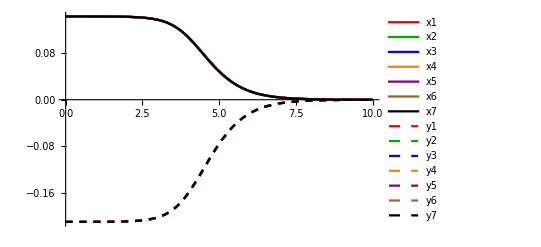

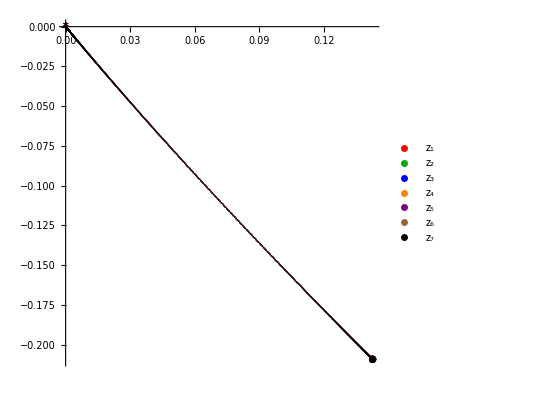

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];(*Export["flowData_SO8_2_to_1.csv",valsBetter,"csv"];*)
```

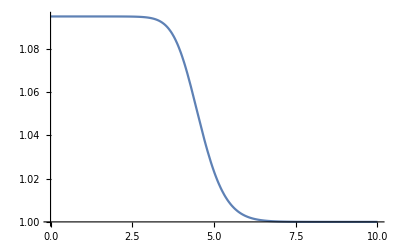

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution,{r, 0, rmax}]
```

## #2 - Direct flow: 3 - 1

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=3;
start=critPointsSigmaSevenScalars[[index]]//N
goalindex=1;
goal=critPointsSigmaSevenScalars[[goalindex]]
```

{0.,0.317837,0.267949,0.,0.,0.317837,0.,0.317837,0.,0.317837,0.267949,0.,0.267949,0.}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit3=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
expansionCrit3RescaledRvalue=expansionCrit3/.{rvalue->Log[10^(-2)]}
```

{-1.56155,-0.561553,0.666667,0.666667,0.666667,1.,1.,1.,1.,1.33333,1.33333,1.33333,2.56155,3.56155}

{0.00466785 α2,0.317837-3.59956×10^-6 α1,0.267949-3.35072×10^-6 α1,0.00712776 α2,0.00466785 α2,0.317837-3.59956×10^-6 α1,0.00466785 α2,0.317837-3.59956×10^-6 α1,0.00466785 α2,0.317837-3.59956×10^-6 α1,0.267949-3.35072×10^-6 α1,0.00712776 α2,0.267949-3.35072×10^-6 α1,0.00712776 α2}

#### Step 1) Find a good initial point by hand

```mathematica
start//N//cut
goal//N//cut
```

{{0.,0.317837},{0.267949,0.},{0.,0.317837},{0.,0.317837},{0.,0.317837},{0.267949,0.},{0.267949,0.}}

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

```mathematica
expansionCrit3
expansionCrit3//TeXForm;
```

{0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.267949-0.362353 2.71828^(2.517 rvalue) α1,0.460507 2.71828^(0.905142 rvalue) α2,0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.267949-0.362353 2.71828^(2.517 rvalue) α1,0.460507 2.71828^(0.905142 rvalue) α2,0.267949-0.362353 2.71828^(2.517 rvalue) α1,0.460507 2.71828^(0.905142 rvalue) α2}

```mathematica
(* Get IC ready *)
ansatz={1,0};
numberOfParams=2;
startIndex=1;
IC = expansionCrit3RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=5;
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* PrecisionGoal->15,PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->10 *)
```

{x1[0]==0.,y1[0]==0.317834,x2[0]==0.267946,y2[0]==0.,x3[0]==0.,y3[0]==0.317834,x4[0]==0.,y4[0]==0.317834,x5[0]==0.,y5[0]==0.317834,x6[0]==0.267946,y6[0]==0.,x7[0]==0.267946,y7[0]==0.}

{0.,3.59956×10^-6,3.35072×10^-6,0.,0.,3.59956×10^-6,0.,3.59956×10^-6,0.,3.59956×10^-6,3.35072×10^-6,0.,3.35072×10^-6,0.}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

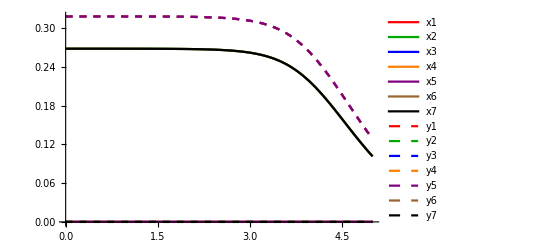

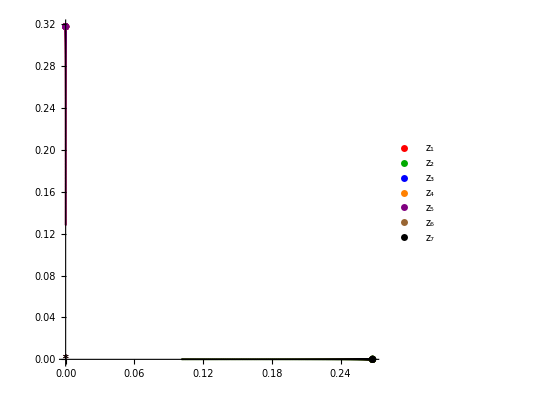

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];(*Export["flowData_SO8_3_to_1_direct.csv",valsBetter,"csv"];*)
```

## #3 - Triangular flow: 3 - 2 - 1

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
checkPointsQ=False;
index=3;
indexRotation=1;
goalindex=2;
indexRotationGoal=2;
(* Get copies for start: *)
start3scComplex=critPoints[[index]];
allStarts3sc=getRotationsCrit[start3scComplex];
allStarts=Table[getSevenFromThree[allStarts3sc[[i]]],{i,1,Length[allStarts3sc]}];
startComplex=allStarts[[indexRotation]];
start=getSigmaFromZ[startComplex]//N
(* Same idea but for goal points *)
goal3scComplex=critPoints[[goalindex]];
allGoals3sc=getRotationsCrit[goal3scComplex];
allGoals=Table[getSevenFromThree[allGoals3sc[[i]]],{i,1,Length[allGoals3sc]}];
goalComplex=allGoals[[indexRotationGoal]];
goal=getSigmaFromZ[goalComplex]//N
```

{0.,0.317837,0.267949,0.,0.,0.317837,0.,0.317837,0.,0.317837,0.267949,0.,0.267949,0.}

{-0.142565,0.209269,0.142565,-0.209269,-0.142565,0.209269,-0.142565,0.209269,-0.142565,0.209269,0.142565,-0.209269,0.142565,-0.209269}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit3=getExpansion[start,eigenvals,eigenvecs]//N//Chop
```

{-1.56155,-0.561553,0.666667,0.666667,0.666667,1.,1.,1.,1.,1.33333,1.33333,1.33333,2.56155,3.56155}

{0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.267949-0.362353 2.71828^(2.517 rvalue) α1,0.460507 2.71828^(0.905142 rvalue) α2,0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.301579 2.71828^(0.905142 rvalue) α2,0.317837-0.389262 2.71828^(2.517 rvalue) α1,0.267949-0.362353 2.71828^(2.517 rvalue) α1,0.460507 2.71828^(0.905142 rvalue) α2,0.267949-0.362353 2.71828^(2.517 rvalue) α1,0.460507 2.71828^(0.905142 rvalue) α2}

```mathematica
(* Modify expansion here *)
expansionCrit3/.{rvalue->Log[10^(-2)]}//cut
expansionCrit3RescaledRvalue=expansionCrit3/.{rvalue->Log[10^(-2)], α1->1};
expansionCrit3RescaledRvalue//cut;
```

{{0.00466785 α2,0.317837-3.59956×10^-6 α1},{0.267949-3.35072×10^-6 α1,0.00712776 α2},{0.00466785 α2,0.317837-3.59956×10^-6 α1},{0.00466785 α2,0.317837-3.59956×10^-6 α1},{0.00466785 α2,0.317837-3.59956×10^-6 α1},{0.267949-3.35072×10^-6 α1,0.00712776 α2},{0.267949-3.35072×10^-6 α1,0.00712776 α2}}

#### Step 1) Find a good initial point by hand

```mathematica
start//N//cut
goal//N//cut
```

{{0.,0.317837},{0.267949,0.},{0.,0.317837},{0.,0.317837},{0.,0.317837},{0.267949,0.},{0.267949,0.}}

{{-0.142565,0.209269},{0.142565,-0.209269},{-0.142565,0.209269},{-0.142565,0.209269},{-0.142565,0.209269},{0.142565,-0.209269},{0.142565,-0.209269}}

```mathematica
(* Get IC ready *)
ansatz={-0.10204624200000002} +0.5* 10^(-10);
numberOfParams=1;
startIndex=2;
IC = expansionCrit3RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=20; (* go until r = 12 to get close to G2 point *)
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* PrecisionGoal->15,PrecisionGoal->15,AccuracyGoal->15,WorkingPrecision->10 *)
```

{x1[0]==-0.000476337,y1[0]==0.317834,x2[0]==0.267946,y2[0]==-0.000727362,x3[0]==-0.000476337,y3[0]==0.317834,x4[0]==-0.000476337,y4[0]==0.317834,x5[0]==-0.000476337,y5[0]==0.317834,x6[0]==0.267946,y6[0]==-0.000727362,x7[0]==0.267946,y7[0]==-0.000727362}

{0.000476337,3.59956×10^-6,3.35072×10^-6,0.000727362,0.000476337,3.59956×10^-6,0.000476337,3.59956×10^-6,0.000476337,3.59956×10^-6,3.35072×10^-6,0.000727362,3.35072×10^-6,0.000727362}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

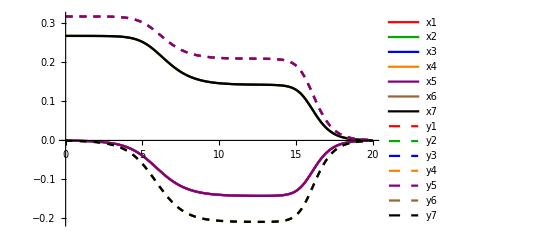

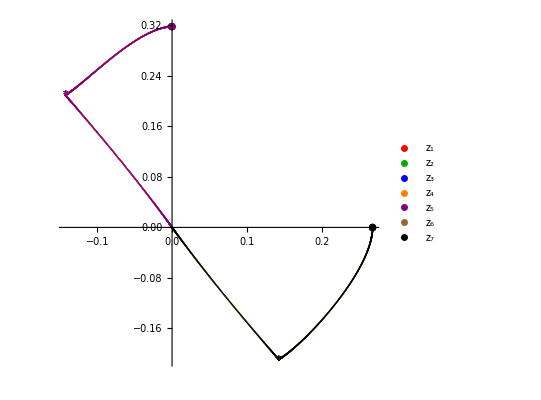

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP3.csv",start,"csv"];*)
(*Export["flowData_SO8_FP2.csv",goal,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_3_to_1.csv",valsBetter,"csv"];*)
```

## Aprime:

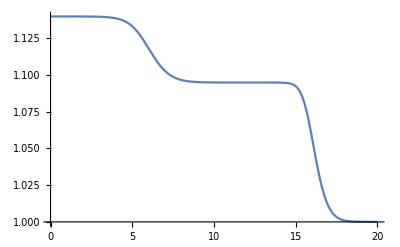

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution,{r, 0, rmax}]
```

## Get flow data of a prime

```mathematica
(* Solution data *)
aprime=Evaluate[aPrimeR/.solution];
aprimevals =Re[aprime/. r ->Subdivide[rmax, 2000]];
aprimevalsBetter =aprimevals[[1]];
(*aprimevalsBetter=Table[aprimevals[[i]][[1]],{i,1,14}];*)
(*Export["flowData_aprime.csv",aprimevalsBetter,"csv"];*)
```

## #4.1 - Flow 4 - 2 - 1, no breaking

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=4;
goalindex=2;
start=critPointsSigmaSevenScalars[[index]]//N
goal=critPointsSigmaSevenScalars[[goalindex]]//N
```

{-0.483321,-0.386406,0.316202,-0.516284,0.169636,0.141574,0.169636,0.141574,0.169636,0.141574,0.316202,-0.516284,0.316202,-0.516284}

{0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit4=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
```

{-2.80254,-1.71632,-0.963244,-0.963244,0.427383,0.427383,0.748735,1.25126,1.57262,1.57262,2.96324,2.96324,3.71632,4.80254}

```mathematica
he=expansionCrit4//cut;
expansionCrit4[[10]]
expansionCrit4//TeXForm;
```

0.141574-0.421996 2.71828^(6.0197 rvalue) α1-0.1449 2.71828^(3.68655 rvalue) α2+0.437792 2.71828^(2.06899 rvalue) α3-0.0217297 2.71828^(2.06899 rvalue) α4

```mathematica
(* Modify expansion here *)
test=expansionCrit4/.{rvalue->Log[10^(-2)]}//cut
expansionCrit4RescaledRvalue=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1};
expansionCrit4NoBreaking=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1, α3->0,α4->0};
expansionCrit4RescaledRvalue//cut;
```

{{-0.483321+1.53878×10^-13 α1+1.55277×10^-8 α2,-0.386406-1.97064×10^-13 α1+1.36199×10^-8 α2},{0.316202+1.14545×10^-14 α1-1.01893×10^-8 α2+0.0000147681 α3-0.000014824 α4,-0.516284+1.48437×10^-14 α1+1.61461×10^-8 α2+0.0000139321 α3-0.0000139849 α4},{0.169636+3.291×10^-13 α1-7.32063×10^-9 α2+1.39323×10^-6 α3-0.0000336724 α4,0.141574-3.85405×10^-13 α1-6.13725×10^-9 α2+1.31241×10^-6 α3-0.0000317192 α4},{0.169636+3.291×10^-13 α1-7.32063×10^-9 α2-0.000035218 α3+0.0000353513 α4,0.141574-3.85405×10^-13 α1-6.13725×10^-9 α2-0.0000331751 α3+0.0000333007 α4},{0.169636+3.291×10^-13 α1-7.32063×10^-9 α2+0.0000338248 α3-1.67889×10^-6 α4,0.141574-3.85405×10^-13 α1-6.13725×10^-9 α2+0.0000318627 α3-1.5815×10^-6 α4},{0.316202+1.14545×10^-14 α1-1.01893×10^-8 α2-5.84226×10^-7 α3+0.00001412 α4,-0.516284+1.48437×10^-14 α1+1.61461×10^-8 α2-5.51155×10^-7 α3+0.0000133207 α4},{0.316202+1.14545×10^-14 α1-1.01893×10^-8 α2-0.0000141838 α3+7.04013×10^-7 α4,-0.516284+1.48437×10^-14 α1+1.61461×10^-8 α2-0.000013381 α3+6.64162×10^-7 α4}}

```mathematica
expansionCrit4NoBreaking
```

{-0.483321+1.53878×10^-13 α1,-0.386406-1.97064×10^-13 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1}

```mathematica
(* Which symmetries are broken along the flow? As expected: alpha 3 and alpha 4 break the symmetry *)
{test[[2]], test[[6]],test[[7]]};
{test[[3]], test[[4]],test[[5]]};
```

#### Step 1) Find a good initial point by hand

```mathematica
start//N//cut
goal//N//cut
```

{{-0.483321,-0.386406},{0.316202,-0.516284},{0.169636,0.141574},{0.169636,0.141574},{0.169636,0.141574},{0.316202,-0.516284},{0.316202,-0.516284}}

{{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269}}

```mathematica
(* Get IC ready *)
ansatz={1.7685999999999997};
numberOfParams=1;
startIndex=1;
IC = expansionCrit4NoBreaking/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=15; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==-0.483321,y1[0]==-0.386406,x2[0]==0.316202,y2[0]==-0.516284,x3[0]==0.169636,y3[0]==0.141574,x4[0]==0.169636,y4[0]==0.141574,x5[0]==0.169636,y5[0]==0.141574,x6[0]==0.316202,y6[0]==-0.516284,x7[0]==0.316202,y7[0]==-0.516284}

{1.5528×10^-8,1.36196×10^-8,1.01893×10^-8,1.61462×10^-8,7.32004×10^-9,6.13793×10^-9,7.32004×10^-9,6.13793×10^-9,7.32004×10^-9,6.13793×10^-9,1.01893×10^-8,1.61462×10^-8,1.01893×10^-8,1.61462×10^-8}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

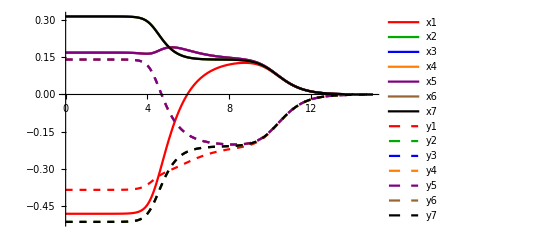

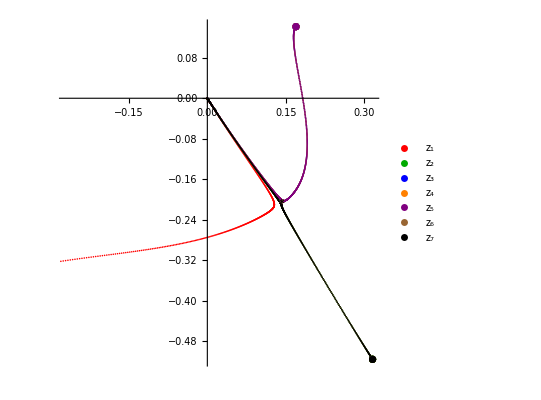

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Aprime:

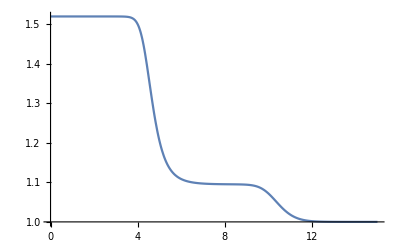

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolutionFirst=Evaluate[aPrimeR/.solution];
aPrimeSolutionFirstPlot=Plot[aPrimeSolutionFirst,{r, 0, rmax}]
```

## #4.2 - Flow 4 - 2 - 1, breaking

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
checkPointsQ=False;
index=4;
indexRotation=1;
goalindex=2;
indexRotationGoal=1;
(* Get copies for start: *)
start3scComplex=critPoints[[index]];
allStarts3sc=getRotationsCrit[start3scComplex];
allStarts=Table[getSevenFromThree[allStarts3sc[[i]]],{i,1,Length[allStarts3sc]}];
startComplex=allStarts[[indexRotation]];
start=getSigmaFromZ[startComplex]//N
(* Same idea but for goal points *)
goal3scComplex=critPoints[[goalindex]];
allGoals3sc=getRotationsCrit[goal3scComplex];
allGoals=Table[getSevenFromThree[allGoals3sc[[i]]],{i,1,Length[allGoals3sc]}];
goalComplex=allGoals[[indexRotationGoal]];
goal=getSigmaFromZ[goalComplex]//N
```

{-0.483321,-0.386406,0.316202,-0.516284,0.169636,0.141574,0.169636,0.141574,0.169636,0.141574,0.316202,-0.516284,0.316202,-0.516284}

{0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit4=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
```

{-2.80254,-1.71632,-0.963244,-0.963244,0.427383,0.427383,0.748735,1.25126,1.57262,1.57262,2.96324,2.96324,3.71632,4.80254}

```mathematica
start//cut
```

{{-0.483321,-0.386406},{0.316202,-0.516284},{0.169636,0.141574},{0.169636,0.141574},{0.169636,0.141574},{0.316202,-0.516284},{0.316202,-0.516284}}

```mathematica
(* Modify expansion here *)
test=expansionCrit4/.{rvalue->Log[10^(-2)]}//cut;
expansionCrit4RescaledRvaluev1=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1};
expansionCrit4RescaledRvaluev2=expansionCrit4RescaledRvaluev1/.{rvalue->Log[10^(-2)], α1->α2};
expansionCrit4RescaledRvaluev2//cut
expansionCrit4RescaledRvalue=expansionCrit4RescaledRvaluev2/.{rvalue->Log[10^(-2)], α3->0.15,α4->0.15};
(* Some scalar pairs are broken now: *)
expansionCrit4RescaledRvalue//cut
```

{{-0.483321+1.53878×10^-13 α2,-0.386406-1.97064×10^-13 α2},{0.316202+1.14545×10^-14 α2+0.0000147681 α3-0.000014824 α4,-0.516284+1.48437×10^-14 α2+0.0000139321 α3-0.0000139849 α4},{0.169636+3.291×10^-13 α2+1.39323×10^-6 α3-0.0000336724 α4,0.141574-3.85405×10^-13 α2+1.31241×10^-6 α3-0.0000317192 α4},{0.169636+3.291×10^-13 α2-0.000035218 α3+0.0000353513 α4,0.141574-3.85405×10^-13 α2-0.0000331751 α3+0.0000333007 α4},{0.169636+3.291×10^-13 α2+0.0000338248 α3-1.67889×10^-6 α4,0.141574-3.85405×10^-13 α2+0.0000318627 α3-1.5815×10^-6 α4},{0.316202+1.14545×10^-14 α2-5.84226×10^-7 α3+0.00001412 α4,-0.516284+1.48437×10^-14 α2-5.51155×10^-7 α3+0.0000133207 α4},{0.316202+1.14545×10^-14 α2-0.0000141838 α3+7.04013×10^-7 α4,-0.516284+1.48437×10^-14 α2-0.000013381 α3+6.64162×10^-7 α4}}

{{-0.483321+1.53878×10^-13 α2,-0.386406-1.97064×10^-13 α2},{0.316202+1.14545×10^-14 α2,-0.516284+1.48437×10^-14 α2},{0.169631+3.291×10^-13 α2,0.141569-3.85405×10^-13 α2},{0.169636+3.291×10^-13 α2,0.141574-3.85405×10^-13 α2},{0.169641+3.291×10^-13 α2,0.141579-3.85405×10^-13 α2},{0.316204+1.14545×10^-14 α2,-0.516282+1.48437×10^-14 α2},{0.3162+1.14545×10^-14 α2,-0.516286+1.48437×10^-14 α2}}

#### Step 1) Find a good initial point by hand

```mathematica
start//N//cut
goal//N//cut
```

{{-0.483321,-0.386406},{0.316202,-0.516284},{0.169636,0.141574},{0.169636,0.141574},{0.169636,0.141574},{0.316202,-0.516284},{0.316202,-0.516284}}

{{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269},{0.142565,-0.209269}}

```mathematica
(* Get IC ready *)
ansatz={9.278569999999991};
numberOfParams=1;
startIndex=2;
IC = expansionCrit4RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=15; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==-0.483321,y1[0]==-0.386406,x2[0]==0.316202,y2[0]==-0.516284,x3[0]==0.169631,y3[0]==0.141569,x4[0]==0.169636,y4[0]==0.141574,x5[0]==0.169641,y5[0]==0.141579,x6[0]==0.316204,y6[0]==-0.516282,x7[0]==0.3162,y7[0]==-0.516286}

{1.55292×10^-8,1.36181×10^-8,1.85735×10^-8,8.23656×10^-9,4.8492×10^-6,4.56715×10^-6,1.26768×10^-8,1.26937×10^-8,4.81457×10^-6,4.53604×10^-6,2.02017×10^-6,1.93158×10^-6,2.03216×10^-6,1.89137×10^-6}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

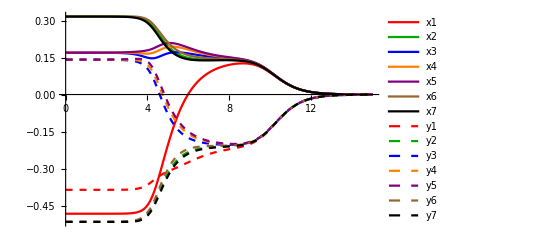

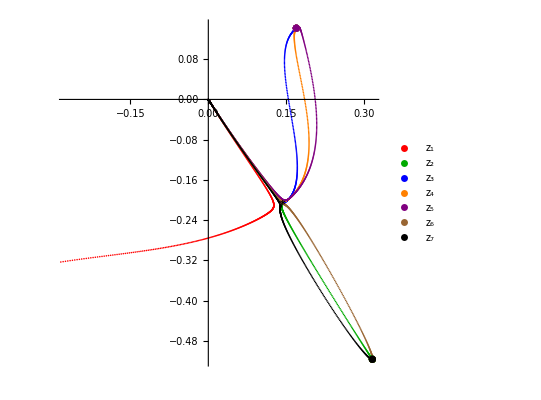

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP4.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_4_to_2_family1.csv",valsBetter,"csv"];*)
```

## Aprime:

Here I compare the A prime plot between the broken and non-broken. They almost coincide! Therefore the A prime plots are, as mentioned in the thesis, not really interesting to consider, especially not since the most important feature of the flows in the larger Z2-cubed truncation is the fact that the scalars can break symmetry - this is not something which leaves an imprint in A prime apparently!

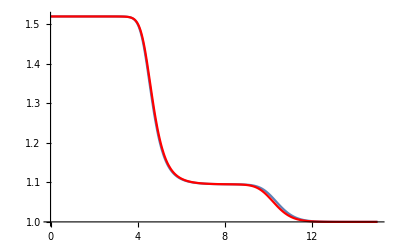

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolutionSecond=Evaluate[aPrimeR/.solution];
aPrimeSolutionSecondPlot=Plot[aPrimeSolutionSecond,{r, 0, rmax},PlotStyle->Red];
Show[aPrimeSolutionFirstPlot,aPrimeSolutionSecondPlot]
```

## #5 - Flows from S12

```mathematica
index=5;
goalindex=1;
start=critPointsSigmaSevenScalars[[index]]//Chop
goal=critPointsSigmaSevenScalars[[goalindex]]
```

{0.366025,-0.366025,0,0,0.366025,0.366025,0.366025,0.366025,-0.366025,0.366025,0,0,0,0.57735}

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit5=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
```

{-1.80588,-1.80588,-1.73205,0.267949,0.643606,0.643606,1.,1.,1.35639,1.35639,1.73205,3.73205,3.80588,3.80588}

```mathematica
(* Modify expansion here *)
test=expansionCrit5/.{rvalue->Log[10^(-2)]}//cut;
expansionCrit5RescaledRvaluev1=expansionCrit5/.{rvalue->Log[10^(-2)]};
expansionCrit5NoBreaking=expansionCrit5/.{rvalue->Log[10^(-2)],α1->0,α2->0};
expansionCrit5RescaledRvaluev2=expansionCrit5RescaledRvaluev1/.{rvalue->Log[10^(-2)]};
expansionCrit5RescaledRvalue=expansionCrit5RescaledRvaluev2;
(* Some scalar pairs are broken now: *)
expansionCrit5RescaledRvalue//cut;
```

```mathematica
expansionCrit5[[13]]
```

0

```mathematica
expansionCrit5
```

{0.366025-0.0472688 2.71828^(3.61177 rvalue) α1-0.217087 2.71828^(3.61177 rvalue) α2+0.319801 2.71828^(3.4641 rvalue) α3,-0.366025-0.0587983 2.71828^(3.61177 rvalue) α1-0.270037 2.71828^(3.61177 rvalue) α2-0.319801 2.71828^(3.4641 rvalue) α3,0.318184 2.71828^(3.61177 rvalue) α1-0.419622 2.71828^(3.61177 rvalue) α2,-0.539002 2.71828^(3.61177 rvalue) α1-0.451521 2.71828^(3.61177 rvalue) α2,0.366025-0.211878 2.71828^(3.61177 rvalue) α1+0.319801 2.71828^(3.4641 rvalue) α3,0.366025+0.263558 2.71828^(3.61177 rvalue) α1+0.319801 2.71828^(3.4641 rvalue) α3,0.366025+0.211878 2.71828^(3.61177 rvalue) α1+0.319801 2.71828^(3.4641 rvalue) α3,0.366025-0.263558 2.71828^(3.61177 rvalue) α1+0.319801 2.71828^(3.4641 rvalue) α3,-0.366025-0.0472688 2.71828^(3.61177 rvalue) α1-0.217087 2.71828^(3.61177 rvalue) α2-0.319801 2.71828^(3.4641 rvalue) α3,0.366025-0.0587983 2.71828^(3.61177 rvalue) α1-0.270037 2.71828^(3.61177 rvalue) α2+0.319801 2.71828^(3.4641 rvalue) α3,-0.500922 2.71828^(3.61177 rvalue) α1-0.419622 2.71828^(3.61177 rvalue) α2,0.342372 2.71828^(3.61177 rvalue) α1-0.451521 2.71828^(3.61177 rvalue) α2,0,0.57735+0.426401 2.71828^(3.4641 rvalue) α3}

```mathematica
(* Checking symmetries and which remain in the expansion *)
test[[3]]
test[[4]]
```

{0.366025-1.26634×10^-8 α1+3.77291×10^-8 α3,0.366025+1.57522×10^-8 α1+3.77291×10^-8 α3}

{0.366025+1.26634×10^-8 α1+3.77291×10^-8 α3,0.366025-1.57522×10^-8 α1+3.77291×10^-8 α3}

```mathematica
test[[2]]
test[[6]]
```

{1.90171×10^-8 α1-2.50797×10^-8 α2,-3.22148×10^-8 α1-2.69863×10^-8 α2}

{-2.99389×10^-8 α1-2.50797×10^-8 α2,2.04627×10^-8 α1-2.69863×10^-8 α2}

```mathematica
test[[5]]
-test[[1]]
```

{-0.366025-2.82514×10^-9 α1-1.29747×10^-8 α2-3.77291×10^-8 α3,0.366025-3.51423×10^-9 α1-1.61395×10^-8 α2+3.77291×10^-8 α3}

{-0.366025+2.82514×10^-9 α1+1.29747×10^-8 α2-3.77291×10^-8 α3,0.366025+3.51423×10^-9 α1+1.61395×10^-8 α2+3.77291×10^-8 α3}

```mathematica
(* Observation: only the perturbation with α3 will respect all symmetries present in the critical point *)
(* Full expansion: *)
test;
```

```mathematica
start//N//cut
goal//N//cut
expansionCrit5NoBreaking//cut;
```

{{0.366025,-0.366025},{0.,0.},{0.366025,0.366025},{0.366025,0.366025},{-0.366025,0.366025},{0.,0.},{0.,0.57735}}

{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}

#### #5.1 - From: S12 - SO(8): direct flow

```mathematica
(* Get IC ready *)
ansatz={-1};
numberOfParams=1;
startIndex=3;
IC =expansionCrit5NoBreaking/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=9; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],60,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==0.366025,y1[0]==-0.366025,x2[0]==0.,y2[0]==0.,x3[0]==0.366025,y3[0]==0.366025,x4[0]==0.366025,y4[0]==0.366025,x5[0]==-0.366025,y5[0]==0.366025,x6[0]==0.,y6[0]==0.,x7[0]==0,y7[0]==0.57735}

{3.77291×10^-8,3.77291×10^-8,0.,0.,3.77291×10^-8,3.77291×10^-8,3.77291×10^-8,3.77291×10^-8,3.77291×10^-8,3.77291×10^-8,0.,0.,0,5.03055×10^-8}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

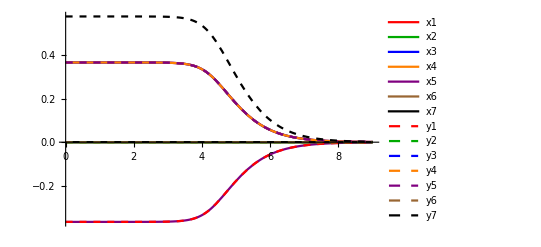

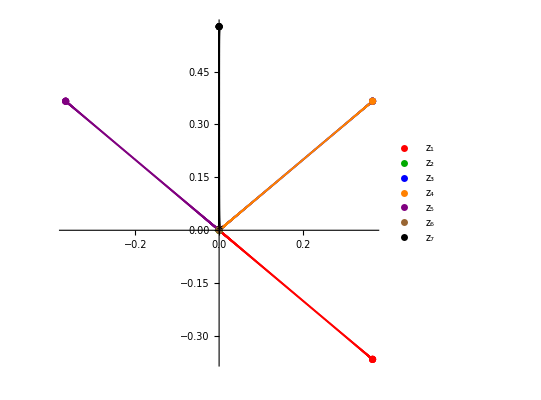

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_5_to_1.csv",valsBetter,"csv"];*)
```

## Aprime:

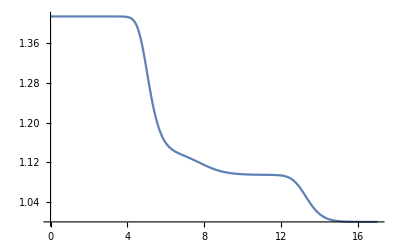

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution1=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution1,{r, 0, rmax}]
```

### #5.2 - Flow: S12 to G2 - completely broken flow, first version:

There’s something fishy - I find more copies of the G2?  EDIT: Yes! This is from the many copies we have! I look for copies at the end of this notebook.

```mathematica
newCritQ={-0.14256483932026498-0.20926947704295434 ⅈ,-0.14256483932026498-0.20926947704295434 ⅈ,0.14256483932026498+0.20926947704295434 ⅈ,0.14256483932026498+0.20926947704295434 ⅈ,-0.14256483932026498-0.20926947704295434 ⅈ,-0.14256483932026498-0.20926947704295434 ⅈ,0.14256483932026498+0.20926947704295434 ⅈ};
```

```mathematica
aCrit=critPointsSevenScalars[[2]];
```

```mathematica
anotherCrit=getRotationsCrit[aCrit]//N;
heya=Table[getSevenFromThree[anotherCrit[[i]]],{i,1,4}]
```

{{-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ},{0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ},{-0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,0.142565+0.209269 ⅈ,0.142565+0.209269 ⅈ,0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ},{0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ}}

```mathematica
anotherCrit=Conjugate[getRotationsCrit[aCrit]]//N;
heya2=Table[getSevenFromThree[anotherCrit[[i]]],{i,1,4}]
```

{{-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,0.142565+0.209269 ⅈ,0.142565+0.209269 ⅈ,0.142565+0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ},{0.142565+0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ},{-0.142565+0.209269 ⅈ,-0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ},{0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565-0.209269 ⅈ,-0.142565-0.209269 ⅈ}}

```mathematica
heyaFull=Join[heya,heya2];
heyaFullCC=heyaFull//Conjugate;
Table[Abs[heyaFull[[i]]-newCritQ],{i,1,Length[heyaFull]}]
Table[Abs[heyaFullCC[[i]]-newCritQ],{i,1,Length[heyaFullCC]}]
```

{{0.418539,0.418539,0.418539,0.418539,0.28513,0.418539,0.28513},{0.28513,0.418539,0.28513,0.28513,0.418539,0.418539,0.28513},{0.,0.418539,0.,0.,0.506432,0.418539,0.28513},{0.506432,0.418539,0.506432,0.506432,0.,0.418539,0.28513},{0.,0.,0.,0.,0.506432,0.,0.506432},{0.506432,0.,0.506432,0.506432,0.,0.,0.506432},{0.418539,0.,0.418539,0.418539,0.28513,0.,0.506432},{0.28513,0.,0.28513,0.28513,0.418539,0.,0.506432}}

{{0.,0.,0.,0.,0.506432,0.,0.506432},{0.506432,0.,0.506432,0.506432,0.,0.,0.506432},{0.418539,0.,0.418539,0.418539,0.28513,0.,0.506432},{0.28513,0.,0.28513,0.28513,0.418539,0.,0.506432},{0.418539,0.418539,0.418539,0.418539,0.28513,0.418539,0.28513},{0.28513,0.418539,0.28513,0.28513,0.418539,0.418539,0.28513},{0.,0.418539,0.,0.,0.506432,0.418539,0.28513},{0.506432,0.418539,0.506432,0.506432,0.,0.418539,0.28513}}

```mathematica
eqs=nablaSS[superpotSevenScalars]/.Join[Table[z[[i]]->newCritQ[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[newCritQ[[i]]],{i,1,7}]]//N//Chop
```

{0,0,0,0,0,0,0}

## Now for the flow itself:

```mathematica
{alpha1Val,alpha2Val}={0.1,0.1};
goal=newCritQ//getSigmaFromZ;
expansionCrit5Breaking=expansionCrit5/.{rvalue->Log[10^(-2)],α1->alpha1Val,α2->alpha2Val};
```

```mathematica
(* Get IC ready *)
ansatz={-0.16258199900000025};
numberOfParams=1;
startIndex=3;
IC =expansionCrit5Breaking/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=17; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==0.366025,y1[0]==-0.366025,x2[0]==-6.06265×10^-10,y2[0]==-5.92011×10^-9,x3[0]==0.366025,y3[0]==0.366025,x4[0]==0.366025,y4[0]==0.366025,x5[0]==-0.366025,y5[0]==0.366025,x6[0]==-5.50186×10^-9,y6[0]==-6.52352×10^-10,x7[0]==0,y7[0]==0.57735}

{7.71406×10^-9,4.16871×10^-9,6.06265×10^-10,5.92011×10^-9,7.40042×10^-9,4.55885×10^-9,4.86773×10^-9,7.7093×10^-9,4.55409×10^-9,8.09944×10^-9,5.50186×10^-9,6.52352×10^-10,0,8.17877×10^-9}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

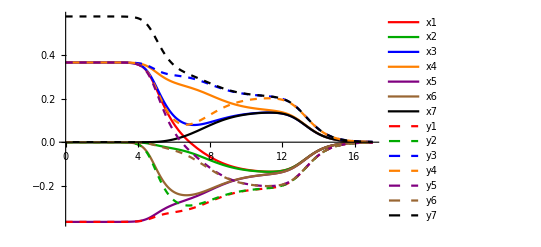

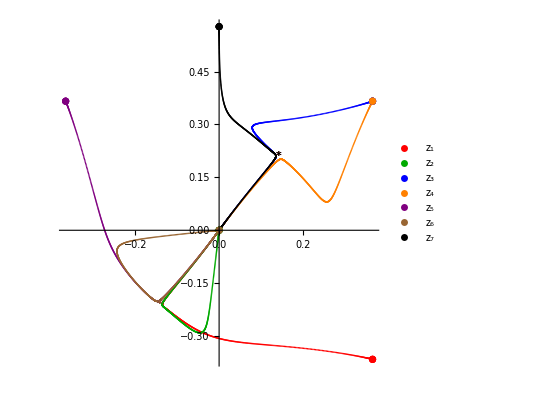

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
G2point=critPointsSigmaSevenScalars[[2]]//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

```mathematica
test=expansionCrit5RescaledRvalue//cut;
test[[4]]
```

{0.366025+1.26634×10^-8 α1+3.77291×10^-8 α3,0.366025-1.57522×10^-8 α1+3.77291×10^-8 α3}

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_5_to_2_triang.csv",valsBetter,"csv"];*)
```

## Aprime:

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution1=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution1,{r, 0, rmax}]
```

-Graphics-

### # 5.3 - Flow: S12 to G2, completely broken but inequivalent

```mathematica
goal=critPointsSigmaSevenScalars[[3]];
{alpha1Val,alpha2Val}={-0.1,-0.1};
expansionCrit5Breaking=expansionCrit5/.{rvalue->Log[10^(-2)],α1->alpha1Val,α2->alpha2Val};
```

```mathematica
newCritQ=Table[0.14256483932026498-0.20926947704295434 ⅈ,7]//Conjugate;
newCritQ=newCritQ//getSigmaFromZ;
```

```mathematica
(* Get IC ready *)
ansatz={-0.16258199900000025};
numberOfParams=1;
startIndex=3;
IC =expansionCrit5Breaking/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=18; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==0.366025,y1[0]==-0.366025,x2[0]==6.06265×10^-10,y2[0]==5.92011×10^-9,x3[0]==0.366025,y3[0]==0.366025,x4[0]==0.366025,y4[0]==0.366025,x5[0]==-0.366025,y5[0]==0.366025,x6[0]==5.50186×10^-9,y6[0]==6.52352×10^-10,x7[0]==0,y7[0]==0.57735}

{4.55409×10^-9,8.09944×10^-9,6.06265×10^-10,5.92011×10^-9,4.86773×10^-9,7.7093×10^-9,7.40042×10^-9,4.55885×10^-9,7.71406×10^-9,4.16871×10^-9,5.50186×10^-9,6.52352×10^-10,0,8.17877×10^-9}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

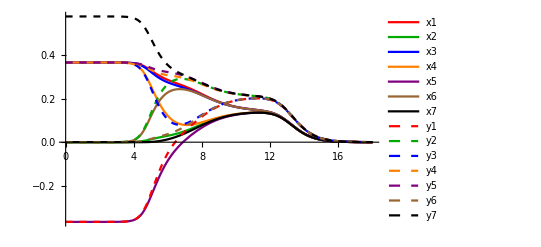

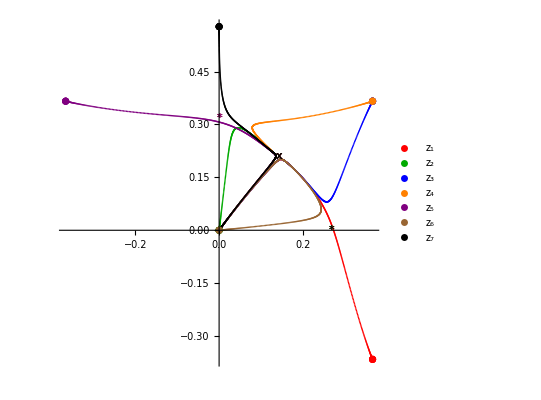

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
G2point=newCritQ//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotG2=ListPlot[{#}&/@G2point,PlotStyle->colorsCF,PlotMarkers->"x"];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal,plotG2]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_5_to_2_triang_v2.csv",valsBetter,"csv"];*)
```

## Aprime:

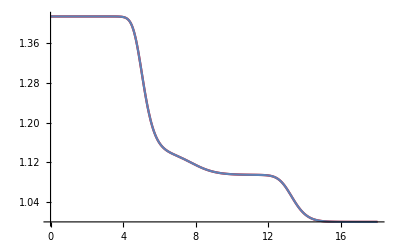

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution2=Evaluate[aPrimeR/.solution];
plot1=Plot[aPrimeSolution2,{r, 0, rmax},PlotStyle->Red];
plot2=Plot[aPrimeSolution1,{r, 0, rmax}];
Show[plot1,plot2]
```

### # 5.4 - STRANGE FLOW

```mathematica
(* Get IC ready *)
ansatz={0.09972999999999999,-0.10070000000000003,-0.13169999999999984};
ansatz={0.09967099999999997,-0.10070000000000003,-0.13169999999999984};
numberOfParams=3;
startIndex=1;
IC = expansionCrit5RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=12;
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];
```

{x1[0]==0.366025,y1[0]==-0.366025,x2[0]==4.42098×10^-9,y2[0]==-4.93364×10^-10,x3[0]==0.366025,y3[0]==0.366025,x4[0]==0.366025,y4[0]==0.366025,x5[0]==-0.366025,y5[0]==0.366025,x6[0]==-4.58509×10^-10,y6[0]==4.75706×10^-9,x7[0]==0,y7[0]==0.57735}

{3.94395×10^-9,6.2439×10^-9,4.42098×10^-9,4.93364×10^-10,6.2311×10^-9,3.39889×10^-9,3.70675×10^-9,6.53896×10^-9,5.9939×10^-9,3.69395×10^-9,4.58509×10^-10,4.75706×10^-9,0,6.62523×10^-9}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

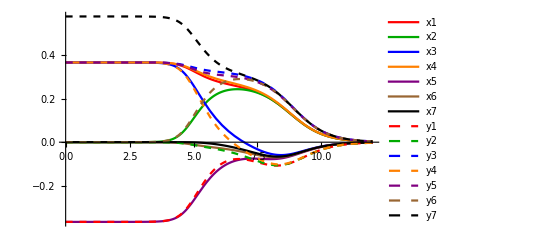

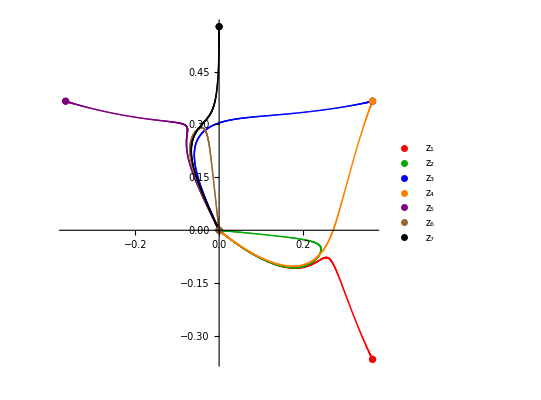

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_5_to_1_strange.csv",valsBetter,"csv"];*)
```

## Aprime:

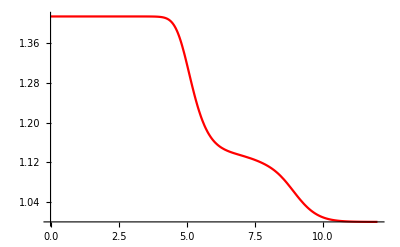

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution2=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution2,{r, 0, rmax},PlotStyle->Red]
```

### # 5.5 - Flow S12 to G2 - no breaking

```mathematica
{alpha1Val,alpha2Val}={0,0.1};
goal=newCritQ//getSigmaFromZ;
expansionCrit5Breaking=expansionCrit5/.{rvalue->Log[10^(-2)],α1->alpha1Val,α2->alpha2Val};
```

```mathematica
(* Get IC ready *)
ansatz={-0.11095212400000001};
numberOfParams=1;
startIndex=3;
IC =expansionCrit5Breaking/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=19; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==0.366025,y1[0]==-0.366025,x2[0]==-2.50797×10^-9,y2[0]==-2.69863×10^-9,x3[0]==0.366025,y3[0]==0.366025,x4[0]==0.366025,y4[0]==0.366025,x5[0]==-0.366025,y5[0]==0.366025,x6[0]==-2.50797×10^-9,y6[0]==-2.69863×10^-9,x7[0]==0,y7[0]==0.57735}

{5.4836×10^-9,2.57218×10^-9,2.50797×10^-9,2.69863×10^-9,4.18613×10^-9,4.18613×10^-9,4.18613×10^-9,4.18613×10^-9,2.88865×10^-9,5.80007×10^-9,2.50797×10^-9,2.69863×10^-9,0,5.5815×10^-9}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

```mathematica
newCritQ={-g2Re-I g2Im,-g2Re-I g2Im,g2Re+I g2Im,g2Re+I g2Im,-g2Re-I g2Im,-g2Re-I g2Im,g2Re+I g2Im};
eqs=nablaSS[superpotSevenScalars];
check=eqs/.Join[Table[z[[i]]->newCritQ[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[newCritQ[[i]]],{i,1,7}]]//Chop
```

{(-ⅈ g2Im-g2Re)^3+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^3 (ⅈ g2Im+g2Re)^3+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (ⅈ Conjugate[g2Im]-Conjugate[g2Re]))/(1-(-ⅈ g2Im-g2Re) (ⅈ Conjugate[g2Im]-Conjugate[g2Re])),(-ⅈ g2Im-g2Re)^3+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^3 (ⅈ g2Im+g2Re)^3+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (ⅈ Conjugate[g2Im]-Conjugate[g2Re]))/(1-(-ⅈ g2Im-g2Re) (ⅈ Conjugate[g2Im]-Conjugate[g2Re])),2 (-ⅈ g2Im-g2Re)^2+4 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+(ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^2+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (-ⅈ Conjugate[g2Im]+Conjugate[g2Re]))/(1-(ⅈ g2Im+g2Re) (-ⅈ Conjugate[g2Im]+Conjugate[g2Re])),2 (-ⅈ g2Im-g2Re)^2+4 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+(ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^2+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (-ⅈ Conjugate[g2Im]+Conjugate[g2Re]))/(1-(ⅈ g2Im+g2Re) (-ⅈ Conjugate[g2Im]+Conjugate[g2Re])),(-ⅈ g2Im-g2Re)^3+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^3 (ⅈ g2Im+g2Re)^3+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (ⅈ Conjugate[g2Im]-Conjugate[g2Re]))/(1-(-ⅈ g2Im-g2Re) (ⅈ Conjugate[g2Im]-Conjugate[g2Re])),(-ⅈ g2Im-g2Re)^3+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)+3 (-ⅈ g2Im-g2Re) (ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^3 (ⅈ g2Im+g2Re)^3+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (ⅈ Conjugate[g2Im]-Conjugate[g2Re]))/(1-(-ⅈ g2Im-g2Re) (ⅈ Conjugate[g2Im]-Conjugate[g2Re])),2 (-ⅈ g2Im-g2Re)^2+4 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+(ⅈ g2Im+g2Re)^2+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^2+((1+(-ⅈ g2Im-g2Re)^4+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)+6 (-ⅈ g2Im-g2Re)^2 (ⅈ g2Im+g2Re)^2+(ⅈ g2Im+g2Re)^3+(-ⅈ g2Im-g2Re)^4 (ⅈ g2Im+g2Re)^3) (-ⅈ Conjugate[g2Im]+Conjugate[g2Re]))/(1-(ⅈ g2Im+g2Re) (-ⅈ Conjugate[g2Im]+Conjugate[g2Re]))}

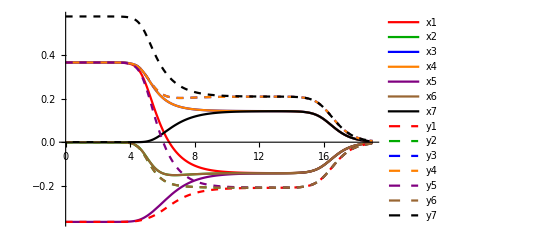

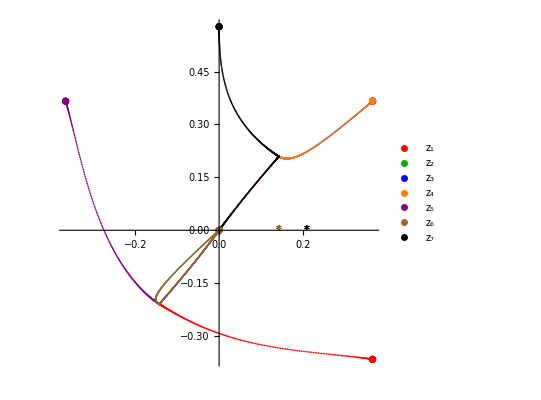

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
G2point=critPointsSigmaSevenScalars[[2]]//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_5_to_2_no_breaking.csv",valsBetter,"csv"];*)
```

## Aprime:

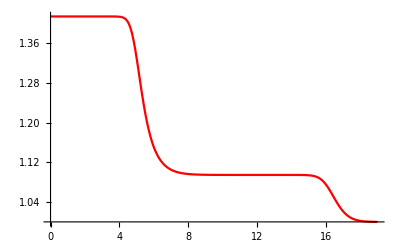

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution2=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution2,{r, 0, rmax},PlotStyle->Red]
```

### Comment On the non-existence of a flow from U(1) x U(1) to SU(3) x U(1)

Ignore this for the following flow (interesting in itself but not here)

```mathematica
{g2Re,g2Im}={0.14256483932026498,0.20926947704295434};
newCritQComplex={-g2Re-I g2Im,-g2Re-I g2Im,g2Re+I g2Im,g2Re+I g2Im,-g2Re-I g2Im,-g2Re-I g2Im,g2Re+I g2Im};
newCritQComplex={g2Re-I g2Im,g2Re-I g2Im,-g2Re+I g2Im,g2Re-I g2Im,-g2Re+I g2Im,-g2Re+I g2Im,-g2Re+I g2Im}
newCritQ=getSigmaFromZ[newCritQComplex];
goal=newCritQ;
eqs=nablaSS[superpotSevenScalars];
eqs/.Join[Table[z[[i]]->newCritQComplex[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[newCritQComplex[[i]]],{i,1,7}]]//N//Chop
```

{0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ}

{0,0,0,0,0,0,0}

THIS is something interesting!!!

```mathematica
critPointsSevenScalars[[3]]//N;
{crit3Re,crit3Im}={0.2679491924311228,0.31783724519578294 I};
newCritQ={crit3Re,crit3Re,crit3Im,crit3Re,crit3Im,crit3Im,crit3Im}
newCritQSigma=newCritQ//getSigmaFromZ;
goal=newCritQSigma;
eqs=nablaSS[superpotSevenScalars];
eqs/.Join[Table[z[[i]]->newCritQComplex[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[newCritQComplex[[i]]],{i,1,7}]]//N//Chop
potentialSevenScalars/.Join[Table[z[[i]]->newCritQ[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[newCritQ[[i]]],{i,1,7}]]//N//Chop
```

{0.267949,0.267949,0.+0.317837 ⅈ,0.267949,0.+0.317837 ⅈ,0.+0.317837 ⅈ,0.+0.317837 ⅈ}

{0,0,0,0,0,0,0}

-7.79423

Good IC:  0.1, -0.1313, -0.1 at rmax = 6

```mathematica
(* Other possible goal: *)
newCritQComplex={g2Re-I g2Im,g2Re-I g2Im,-g2Re+I g2Im,g2Re-I g2Im,-g2Re+I g2Im,-g2Re+I g2Im,-g2Re+I g2Im}
newCritQ=getSigmaFromZ[newCritQComplex];
goal=newCritQ; (* -0.1314950000000003at rm = 8.6 *)
{alpha1Val,alpha2Val}={0.1,-0.1};
{crit3Re,crit3Im}={0.2679491924311228,0.31783724519578294 I};
newCritQ={crit3Re,crit3Re,crit3Im,crit3Re,crit3Im,crit3Im,crit3Im}
newCritQSigma=newCritQ//getSigmaFromZ;
(* Choose goal *)
goal=newCritQ//getSigmaFromZ;
expansionCrit5Breaking=expansionCrit5/.{rvalue->Log[10^(-2)],α1->alpha1Val,α2->alpha2Val};
```

{0.142565-0.209269 ⅈ,0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,0.142565-0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ,-0.142565+0.209269 ⅈ}

{0.267949,0.267949,0.+0.317837 ⅈ,0.267949,0.+0.317837 ⅈ,0.+0.317837 ⅈ,0.+0.317837 ⅈ}

```mathematica
(* Get IC ready *)
ansatz={0.09972999999999999,-0.10070000000000003,-0.13169999999999984}; (* this until 6.7 was best for SU(3) x U(1) *)
numberOfParams=3;
startIndex=1;
IC =expansionCrit5RescaledRvalue/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=7; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==0.366025,y1[0]==-0.366025,x2[0]==4.42211×10^-9,y2[0]==-4.95265×10^-10,x3[0]==0.366025,y3[0]==0.366025,x4[0]==0.366025,y4[0]==0.366025,x5[0]==-0.366025,y5[0]==0.366025,x6[0]==-4.60275×10^-10,y6[0]==4.75827×10^-9,x7[0]==0,y7[0]==0.57735}

{0.849347,0.0203804,0.316202,0.516284,0.196389,0.224451,0.196389,0.224451,0.535661,0.224451,0.316202,0.516284,0.316202,1.09363}

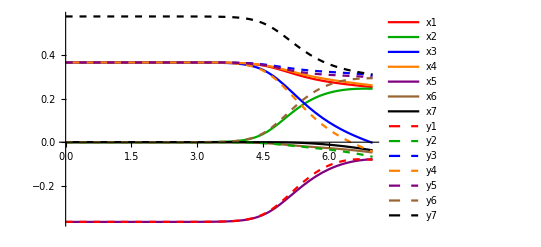

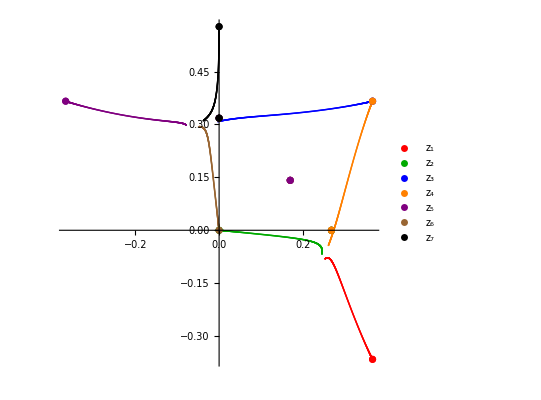

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotStart,plotGoal]
```

```mathematica
NumberForm[goal,12]
```

{0.267949192431,0,0.267949192431,0,0.,0.317837245196,0.267949192431,0,0.,0.317837245196,0.,0.317837245196,0.,0.317837245196}

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_conjectured.csv",valsBetter,"csv"];*)
```

## #6 SO(3) to SO(8)

```mathematica
(* CHOOSE ORIGIN AND TARGET *)
index=4;
goalindex=2;
start=critPointsSigmaSevenScalars[[index]]//N
goal=critPointsSigmaSevenScalars[[goalindex]]//N
```

{-0.483321,-0.386406,0.316202,-0.516284,0.169636,0.141574,0.169636,0.141574,0.169636,0.141574,0.316202,-0.516284,0.316202,-0.516284}

{0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269,0.142565,-0.209269}

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit4=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
```

{-2.80254,-1.71632,-0.963244,-0.963244,0.427383,0.427383,0.748735,1.25126,1.57262,1.57262,2.96324,2.96324,3.71632,4.80254}

```mathematica
(* Modify expansion here *)
test=expansionCrit4/.{rvalue->Log[10^(-2)]}//cut;
expansionCrit4RescaledRvalue=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1};
expansionCrit4NoBreaking=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1, α3->0,α4->0};
expansionCrit4RescaledRvalue//cut;
```

```mathematica
expansionCrit4NoBreaking
```

{-0.483321+1.53878×10^-13 α1,-0.386406-1.97064×10^-13 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1}

```mathematica
(* Get IC ready *)
ansatz={0.1};
numberOfParams=1;
startIndex=1;
IC =expansionCrit4NoBreaking/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=9; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==-0.483321,y1[0]==-0.386406,x2[0]==0.316202,y2[0]==-0.516284,x3[0]==0.169636,y3[0]==0.141574,x4[0]==0.169636,y4[0]==0.141574,x5[0]==0.169636,y5[0]==0.141574,x6[0]==0.316202,y6[0]==-0.516284,x7[0]==0.316202,y7[0]==-0.516284}

{1.55277×10^-8,1.36199×10^-8,1.01893×10^-8,1.61461×10^-8,7.32059×10^-9,6.13729×10^-9,7.32059×10^-9,6.13729×10^-9,7.32059×10^-9,6.13729×10^-9,1.01893×10^-8,1.61461×10^-8,1.01893×10^-8,1.61461×10^-8}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

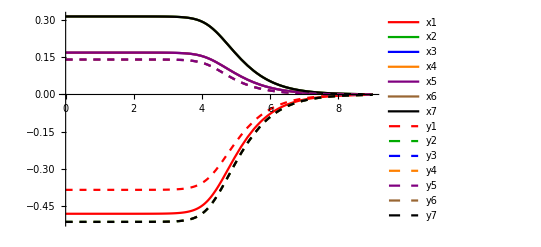

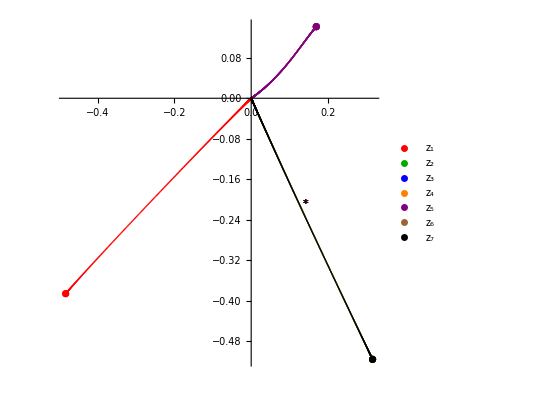

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotGoal]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_4_to_1_direct.csv",valsBetter,"csv"];*)
```

## Aprime:

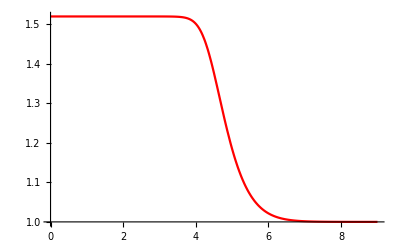

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution2=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution2,{r, 0, rmax},PlotStyle->Red]
```

## #6.2 - Break this flow?

```mathematica
(* Get expansion: *)
jac=getJacobian[start]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[-3/potentialValue];
deltas=eigenvals*(-L);
deltas//N//Sort
(* Get the critical point in the IR and an expansion around it: *)
expansionCrit4=getExpansion[start,eigenvals,eigenvecs]//N//Chop;
```

{-2.80254,-1.71632,-0.963244,-0.963244,0.427383,0.427383,0.748735,1.25126,1.57262,1.57262,2.96324,2.96324,3.71632,4.80254}

```mathematica
(* Modify expansion here *)
test=expansionCrit4/.{rvalue->Log[10^(-2)]}//cut;
expansionCrit4RescaledRvalue=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1};
expansionCrit4Broken=expansionCrit4/.{rvalue->Log[10^(-2)], α2->1, α3->0.3,α4->0.3};
expansionCrit4RescaledRvalue//cut;
```

```mathematica
expansionCrit4Broken
```

{-0.483321+1.53878×10^-13 α1,-0.386406-1.97064×10^-13 α1,0.316202+1.14545×10^-14 α1,-0.516284+1.48437×10^-14 α1,0.169626+3.291×10^-13 α1,0.141565-3.85405×10^-13 α1,0.169636+3.291×10^-13 α1,0.141574-3.85405×10^-13 α1,0.169646+3.291×10^-13 α1,0.141583-3.85405×10^-13 α1,0.316206+1.14545×10^-14 α1,-0.51628+1.48437×10^-14 α1,0.316198+1.14545×10^-14 α1,-0.516288+1.48437×10^-14 α1}

```mathematica
(* Get IC ready *)
ansatz={31.5};
numberOfParams=1;
startIndex=1;
IC =expansionCrit4Broken/.getAlphaRule[ansatz];
(* Gather in a list *)
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,14}]//refine;
IClist
Abs[IC- fpSigma]
(* Solve - rmax is for the range of r *)
rmax=9; 
solution = TimeConstrained[NDSolve[Join[flowEqsSS, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"},WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15],70,Print["Blew up!"]];(* ,WorkingPrecision->50,MaxSteps->20000,AccuracyGoal->15,PrecisionGoal->15 *)
```

{x1[0]==-0.483321,y1[0]==-0.386406,x2[0]==0.316202,y2[0]==-0.516284,x3[0]==0.169626,y3[0]==0.141565,x4[0]==0.169636,y4[0]==0.141574,x5[0]==0.169646,y5[0]==0.141583,x6[0]==0.316206,y6[0]==-0.51628,x7[0]==0.316198,y7[0]==-0.516288}

{1.55326×10^-8,1.36137×10^-8,2.69576×10^-8,3.27171×10^-10,9.69107×10^-6,9.12817×10^-6,3.26785×10^-8,3.15197×10^-8,9.63646×10^-6,9.07821×10^-6,4.05053×10^-6,3.84701×10^-6,4.05414×10^-6,3.7989×10^-6}

NDSolve::precw: The precision of the differential equation ({{<<28>>}, {}, {}, {}, {}}) is less than WorkingPrecision (50.).

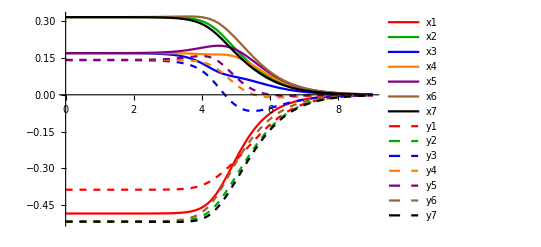

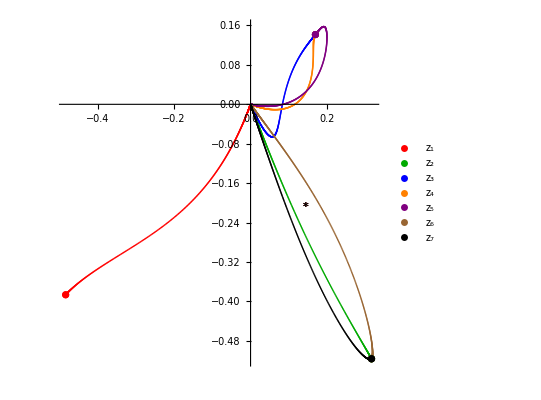

```mathematica
(* Get the values now *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
reScalars=Evaluate[Table[xR[[i]]/. solution,{i, 1,7}]];
imScalars=Evaluate[Table[yR[[i]]/. solution,{i, 1,7}]];
(* Get the x and y values, save them as "coordinates" in the complex plane *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
solutionsRF= Table[vals[[i]][[1]],{i,1,14}];
solutionsComplex=Table[Transpose@{solutionsRF[[2*i-1]],solutionsRF[[2*i]]},{i,1,7}];
(* Make the plots *)
plotAllScalars=Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]];
plotComplexScalars=ListPlot[solutionsComplex,mystyleComplex];
plotReScalars=Plot[reScalars,{r, 0, rmax},Evaluate[mystyleReScalars]];
plotImScalars=Plot[imScalars,{r, 0, rmax},Evaluate[mystyleImScalars]];
ICcut=IC//cut;
startcut=start//cut;
goalcut=goal//cut;
plotIC=ListPlot[{#}&/@ICcut,PlotStyle->colorsCF];
plotStart=ListPlot[{#}&/@startcut,PlotStyle->colorsCF];
plotGoal=ListPlot[{#}&/@goalcut,PlotStyle->colorsCF,PlotMarkers->"*"];
(* Show desired plots *)
Show[plotReScalars,plotImScalars]
Show[plotComplexScalars,plotIC,plotGoal]
```

## Get flow data

```mathematica
(* Fixed point data *)
(*Export["flowData_SO8_FP5.csv",start,"csv"];*)
```

```mathematica
(* Solution data *)
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1,14}]];
vals =Re[funcs/. r ->Subdivide[rmax, 2000]];
valsBetter=Table[vals[[i]][[1]],{i,1,14}];
(*Export["flowData_SO8_4_to_1_broken.csv",valsBetter,"csv"];*)
```

## Aprime:

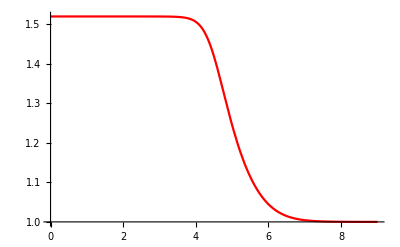

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotSevenScalars]*Exp[kahlerpotSevenScalars/2]//complexToRealScalars//N;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution2=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution2,{r, 0, rmax},PlotStyle->Red]
```

## ==================================== To Do ====================================

## =========================== Extra: looking for copies ===============================================================

```mathematica
superpotSevenScalars
```

1+z1 z2 z4+z2 z3 z5+z1 z3 z4 z5+z1 z3 z6+z2 z3 z4 z6+z1 z2 z5 z6+z4 z5 z6+z1 z2 z3 z7+z3 z4 z7+z1 z5 z7+z2 z4 z5 z7+z2 z6 z7+z1 z4 z6 z7+z3 z5 z6 z7+z1 z2 z3 z4 z5 z6 z7

Motivational example:

```mathematica
newSuperpotSevenScalars=superpotSevenScalars/.{z1->z6,z6->z1,z4->z7,z7->z4};
diff=superpotSevenScalars-newSuperpotSevenScalars
```

0

Find all permutations that are relevant to us.

```mathematica
allPermutations=AlternatingGroup[7]//GroupElements;
allPermutations//Dimensions
```

{2520}

```mathematica
Permute[z,permutations[[1]]]
```

Part::partd: Part specification permutations⟦1⟧ is longer than depth of object.

Permute[{z1,z2,z3,z4,z5,z6,z7},permutations⟦1⟧]

```mathematica
(* Go over all permutations: *)
symmPerm={};
For[i=1,i<Length[allPermutations]+1,i++,
(
perm=allPermutations[[i]];
zPerm=Permute[z,perm];
newSuperpotSevenScalars=superpotSevenScalars/.Table[z[[j]]->zPerm[[j]],{j,1,7}];
diff=superpotSevenScalars-newSuperpotSevenScalars//Simplify;
If[diff==0,AppendTo[symmPerm,perm]];
)];
```

```mathematica
symmPerm//Dimensions
```

{168}

Sign flips: first get all sign flips (exclude 0 and 7 sign flips: 0 = trivial, 7 = non-invariant)

```mathematica
(* Get all vectors containing the sign flips: *)
allSignFlipVectors={};
For[i=1,i<Length[allPermutations]+1,i++,
(
perm=allPermutations[[i]];
(* 1 minus sign *)
vector={-1,1,1,1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 2 minus sign *)
vector={-1,-1,1,1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 3 minus sign *)
vector={-1,-1,-1,1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 4 minus sign *)
vector={-1,-1,-1,-1,1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 5 minus sign *)
vector={-1,-1,-1,-1,-1,1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
(* 6 minus sign *)
vector={-1,-1,-1,-1,-1,-1,1};
vecPerm=Permute[vector,perm];
AppendTo[allSignFlipVectors,vecPerm];
)];
allSignFlipVectors=allSignFlipVectors//DeleteDuplicates;
```

```mathematica
allSignFlipVectors//Dimensions
```

{126,7}

Now check which ones leave the superpotential invariant

```mathematica
test=allSignFlipVectors[[2]]
```

{-1,-1,1,1,1,1,1}

```mathematica
goodSignFlipVectors={};
For[a=1,a<Length[allSignFlipVectors]+1,a++,
(
signFlipVector=allSignFlipVectors[[a]];
newZ=signFlipVector*z;
newSuperpotSevenScalars=superpotSevenScalars/.Table[z[[i]]->newZ[[i]],{i,1,7}];
diff=superpotSevenScalars-newSuperpotSevenScalars;
If[diff==0,AppendTo[goodSignFlipVectors,signFlipVector]];
)];
```

```mathematica
goodSignFlipVectors//Dimensions
```

{7,7}

```mathematica
goodSignFlipVectors
```

{{-1,-1,-1,1,1,1,-1},{-1,-1,1,1,-1,-1,1},{-1,1,-1,-1,-1,1,1},{-1,1,1,-1,1,-1,-1},{1,-1,-1,-1,1,-1,1},{1,-1,1,-1,-1,1,-1},{1,1,-1,1,-1,-1,-1}}

Now find as many inequivalent copies as possible:

```mathematica
allCritLists={};
For[b=1,b<7,b++,
(
(* Do one additional entry where we consider an arbitrary z , otherwise take a crit point *)
If[b==6,aCrit=complexToRealScalars[z],aCrit=critPointsSevenScalars[[b]];];
aCritCC=aCrit//Conjugate//ComplexExpand;
aCritList={};
(* 1 - get SF *)
SFlist={};
For[a=1,a<Length[goodSignFlipVectors]+1,a++,
(
(* get current sign flip *)
signflip=goodSignFlipVectors[[a]];
(* flip the crit *)
newCrit=signflip*aCrit;
AppendTo[aCritList,newCrit];
AppendTo[SFlist,newCrit];
(* flip its CC *)
newCrit=signflip*aCritCC;
AppendTo[aCritList,newCrit];
AppendTo[SFlist,newCrit];
)];
(* 2 - get P *)
Plist={};
For[a=1,a<Length[symmPerm]+1,a++,
(
(* get current permutation *)
perm=symmPerm[[a]];
(* permute the crit *)
newCrit=Permute[aCrit,perm];
AppendTo[aCritList,newCrit];
AppendTo[Plist,newCrit];
(* permute its CC *)
newCrit=Permute[aCritCC,perm];
AppendTo[aCritList,newCrit];
AppendTo[Plist,newCrit];
)];
(* 3 - get SF[P] *)
For[p=1,p<Length[Plist]+1,p++,
(
currentCrit=Plist[[p]];
(* Get a point from Plist, and flip its signs *)
For[a=1,a<Length[goodSignFlipVectors]+1,a++,
(
(* get current sign flip *)
signflip=goodSignFlipVectors[[a]];
(* flip the crit *)
newCrit=signflip*currentCrit;
AppendTo[aCritList,newCrit];
)];
)];
(* 4 - get P[SF] *)
For[p=1,p<Length[SFlist]+1,p++,
(
currentCrit=SFlist[[p]];
(* Get a point from Plist, and flip its signs *)
For[a=1,a<Length[symmPerm]+1,a++,
(
(* get current permutation *)
perm=symmPerm[[a]];
(* permute the crit *)
newCrit=Permute[currentCrit,perm];
AppendTo[aCritList,newCrit];
)];
)];
aCritList=aCritList//DeleteDuplicates;
AppendTo[allCritLists,aCritList]);
];
```

```mathematica
(* get number of distinct copies. Note: final value is the order of the symmetry group? *)
Table[Length[allCritLists[[f]]],{f,1,Length[allCritLists]}]
```

{1,16,56,448,672,2688}

## New code:

```mathematica
(* Take a crit. This is fixed throughout the exploration *)
For[b=1,b<6,b++,
((* For each b means for each crit (there are 5) *)
toCheckCrits=allCritLists[[b]];
(* Build towards the to check *)
eqs=nablaSS[superpotSevenScalars];
permutedCrits={};
For[a=1,a<Length[toCheckCrits]+1,a++,
(
(* Now check each distinct copy. Take it: *)
currentCrit=toCheckCrits[[a]];
(* Check if it is a susy vacuum *)
check=eqs/.Join[Table[z[[i]]->currentCrit[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[currentCrit[[i]]],{i,1,7}]]//N//Chop;
If[check=={0,0,0,0,0,0,0},AppendTo[permutedCrits,currentCrit]];
)];
numberOfCritsEstimate=Length[DeleteDuplicates[permutedCrits]];
Print[StringForm["There are at least `` susy copies for critical point ``",numberOfCritsEstimate,b]];
)];
```

There are at least 1 susy copies for critical point 1

There are at least 16 susy copies for critical point 2

There are at least 56 susy copies for critical point 3

There are at least 448 susy copies for critical point 4

There are at least 672 susy copies for critical point 5

## Old code:

```mathematica
(* Take a crit. This is fixed throughout the exploration *)
For[b=1,b<6,b++,
(
aCrit=critPointsSevenScalars[[b]];
orbitCrits=Table[goodSignFlipVectors[[o]]*aCrit,{o,1,Length[goodSignFlipVectors]}];
toCheckCrits={aCrit,Conjugate[aCrit]}//Flatten;
(* NEWWW *)
toCheckCrits=allCritLists[[b]];
(* Build towards the to check *)
eqs=nablaSS[superpotSevenScalars];
check=Table[eqs/.Join[Table[z[[i]]->orbitCrits[[h]][[i]],{i,1,7}],Table[zb[[i]]->Conjugate[orbitCrits[[h]][[i]]],{i,1,7}]]//N//Chop,{h,1,Length[orbit]}];
permutedCrits={};
For[a=1,a<4,a++,
(currentCrit=toCheckCrits[[a]];
For[k=1,k<Length[symmPerm]+1,k++,
(
perm=symmPerm[[k]];
anotherCritQ=Permute[aCrit,perm];
(* Check if it is a susy vacuum *)
check=eqs/.Join[Table[z[[i]]->anotherCritQ[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[anotherCritQ[[i]]],{i,1,7}]]//N//Chop;
If[Norm[Abs[check]]<10^(-8),AppendTo[permutedCrits,anotherCritQ]];
(* Check if it is a non-susy vacuum *)
(*checkPotential=eqsPotential/.Join[Table[z[[i]]->anotherCritQ[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[anotherCritQ[[i]]],{i,1,7}]]//N//Chop;*)
(*If[Norm[Abs[checkPotential]]<10^(-8),AppendTo[permutedCritsPotential,anotherCritQ]];*)
)];
)];
numberOfCritsEstimate=Length[DeleteDuplicates[permutedCrits]];
Print[StringForm["There are at least `` susy copies for critical point ``",numberOfCritsEstimate,b]];
)];
```

Part::partw: Part 2 of {{0.,0.,0.,0.,0.,0.,0.}} does not exist.

Part::partw: Part 3 of {{0.,0.,0.,0.,0.,0.,0.}} does not exist.

There are at least 1 susy copies for critical point 1

There are at least 1 susy copies for critical point 2

There are at least 7 susy copies for critical point 3

There are at least 28 susy copies for critical point 4

There are at least 84 susy copies for critical point 5

Note: for practical reasons we have a reversed order: critical point 5 is the U(1) x U(1) point, 4 is SO(3). We also checked for the possibility that some susy vacua mapped with the above symmetries to non-susy-vacua.

2352

```mathematica
{g2Re,g2Im}={0.14256483932026498,0.20926947704295434};
g2crit1={-g2Re+I g2Im,g2Re-I g2Im,-g2Re+I g2Im,-g2Re+I g2Im,-g2Re+I g2Im,g2Re-I g2Im,g2Re-I g2Im};
check=eqs/.Join[Table[z[[i]]->g2crit1[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[g2crit1[[i]]],{i,1,7}]]//N//Chop
g2crit2={-g2Re-I g2Im,-g2Re-I g2Im,g2Re+I g2Im,g2Re+I g2Im,-g2Re-I g2Im,-g2Re-I g2Im,g2Re+I g2Im};
check=eqs/.Join[Table[z[[i]]->g2crit2[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[g2crit2[[i]]],{i,1,7}]]//N//Chop
test1=Conjugate[g2crit1];
check=eqs/.Join[Table[z[[i]]->test1[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[test1[[i]]],{i,1,7}]]//N//Chop
test2=Conjugate[g2crit2];
check=eqs/.Join[Table[z[[i]]->test2[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[test2[[i]]],{i,1,7}]]//N//Chop
test3={-g2crit1[[1]],g2crit1[[2]],-g2crit1[[3]],-g2crit1[[4]],-g2crit1[[5]],g2crit1[[6]],g2crit1[[7]]};
check=eqs/.Join[Table[z[[i]]->test3[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[test3[[i]]],{i,1,7}]]//N//Chop
test4={-g2crit2[[1]],g2crit2[[2]],-g2crit2[[3]],-g2crit2[[4]],-g2crit2[[5]],g2crit2[[6]],g2crit2[[7]]};
check=eqs/.Join[Table[z[[i]]->test4[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[test4[[i]]],{i,1,7}]]//N//Chop
(* All are critical points! Save them *)
allG2CritsNoPermutations={g2crit1,g2crit2,test1,test2,test3,test4};
```

{0,0,0,0,0,0,0}

{0,0,0,0,0,0,0}

{0,0,0,0,0,0,0}

«3 more identical outputs»

```mathematica
(* Did we find these in our symmetry based search above?? *)
Table[MemberQ[allCritLists[[2]],allG2CritsNoPermutations[[i]]],{i,1,6}]
```

{True,True,True,True,True,True}

```mathematica
(* For the G2, we need more work, as the crit reported in the thesis is clearly not giving all options. *)
toCheckCrits=allG2CritsNoPermutations;
eqs=nablaSS[superpotSevenScalars];
permutedCrits={};
counter=0;
For[a=1,a<Length[toCheckCrits]+1,a++,
(currentCrit=toCheckCrits[[a]];
For[k=1,k<Length[symmPerm]+1,k++,
(
perm=symmPerm[[k]];
anotherCritQ=Permute[aCrit,perm];
check=eqs/.Join[Table[z[[i]]->anotherCritQ[[i]],{i,1,7}],Table[zb[[i]]->Conjugate[anotherCritQ[[i]]],{i,1,7}]]//N//Chop;
If[check=={0,0,0,0,0,0,0},
(counter=counter+1;
AppendTo[permutedCrits,anotherCritQ];
)];
)];
)];
numberOfCritsEstimate=Length[DeleteDuplicates[permutedCrits]];
Print[StringForm["There are at least `` copies for the G2 point",numberOfCritsEstimate]];
```

There are at least 84 copies for the G2 point

# === Archive: finetuning by hand in the 3 scalar model ===

## Holographic RG flows

### Getting the equations

```mathematica
(* Get the flow equations for the REAL scalars. Rescale such that g no longer appears *)
xprimeR3sc=xprime//putRDependence/.{g->1/Sqrt[2]};
yprimeR3sc=yprime//putRDependence/.{g->1/Sqrt[2]};
sigmaprimeR3sc=Transpose[{xprimeR3sc,yprimeR3sc}]//Flatten;
(* Get the flow equations for the real scalars to be solved WATCH OUT FOR THE SIGN HERE!!! *)
flowEqs3sc=Table[D[sigmaR[[i]],r]-sigmaprimeR3sc[[i]]==0,{i,1,6}];
sigma3sc=Table[sigma[[i]],{i,1,6}];
```

### Triangular flow from SO(3) to the origin

```mathematica
(* Get the initial condition *)
index = 4;
startVec=critPointsSigma[[index]];
jac=jacobiansNum[[index]];
Eigenvalues[jac];
eigenvec=Eigenvectors[jac];
eps=10^-2;
(* Getting the triangular flow depends on the ratio of how much we activate some of the modes: determined by alpha below. Alpha must surely be smaller than 0.132 alpha = 0.1 or something gives regular flows *)
alpha=0.1311951;
epsVector=eps*{0,0,alpha,-1,0,0};
etaVector=Sum[epsVector[[i]]*eigenvec[[i]],{i,1,Length[epsVector]}];
IC=startVec+etaVector;
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,6}]
```

{x1[0]==0.171984,y1[0]==0.141952,x2[0]==0.485643,y2[0]==0.389074,x3[0]==-0.321149,y3[0]==0.523944}

$Aborted

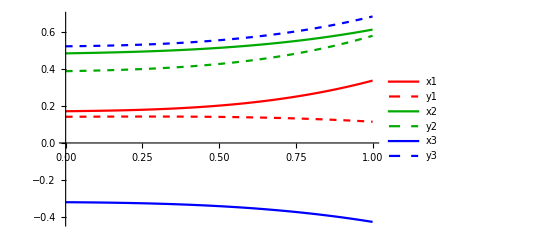

```mathematica
(* Solve - rmax is for the range of r *)
rmax=1;
solution = NDSolve[Join[flowEqs3sc, IClist],sigma3sc,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"}, WorkingPrecision->MachinePrecision];
funcs=Evaluate[Table[sigmaR[[i]]/. solution,{i, 1, 6}]];
Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]]
```

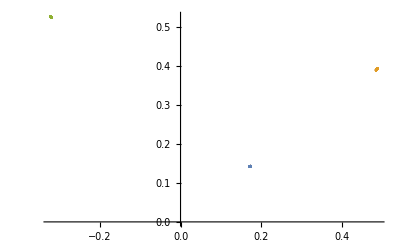

```mathematica
(* Get the x and y values, save them as "coordinates *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
{x1vals,y1vals,x2vals,y2vals,x3vals,y3vals} = Table[vals[[i]][[1]],{i,1,6}];
{vals1,vals2,vals3}={Transpose@{x1vals,y1vals},Transpose@{x2vals,y2vals},Transpose@{x3vals,y3vals}};
plotComplexScalars=ListPlot[{vals1,vals2,vals3}];
Show[plotComplexScalars](* ,plotCriticalPoints,plotArrows4*)
```

```mathematica
Sqrt[2]//N
```

1.41421

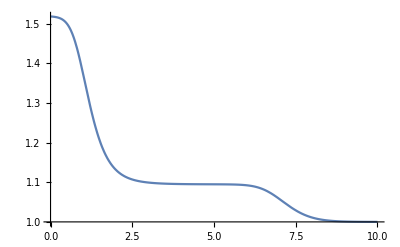

```mathematica
(* Also plot Aprime along this flow *)
aPrime=Abs[superpotPaper]*Exp[kahlerpotPaper/2]//complexToRealScalars//ComplexExpand;
aPrimeR=aPrime //putRDependence;
(*Show A' along the flow*)
aPrimeSolution=Evaluate[aPrimeR/.solution];
Plot[aPrimeSolution,{r, 0, rmax}]
```

### The other triangular flow from SO(3) to the origin

```mathematica
(* Get the initial condition *)
index = 4;
startVec=critPointsSigma[[index]];
eigenvals[[index]];
eigenvec=eigenvecs[[index]];
eps=10^-2;
(* Getting the triangular flow depends on the ratio of how much we activate some of the modes: determined by beta below. Must be smaller than 0.10997 *)
beta=0.1099555;
epsVector=eps*{0,0,-beta,-1,0,0};
etaVector=Sum[epsVector[[i]]*eigenvec[[i]],{i,1,Length[epsVector]}];
IC=startVec+etaVector;
IClist=Table[sigmaZero[[i]]==IC[[i]],{i,1,Length[sigmaZero]}];
```

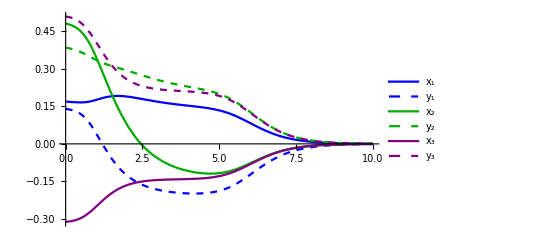

```mathematica
(* Solve - rmax is for the range of r *)
rmax=10;
s = NDSolve[Join[flowEqs, IClist],sigma,{r, 0, rmax},Method->{"EquationSimplification"->"Solve"}];
funcs=Evaluate[Table[sigmaR[[i]]/. s,{i, 1, 2*nscalarsPaper}]];
Plot[funcs,{r, 0, rmax},Evaluate[mystyleReal]]
```

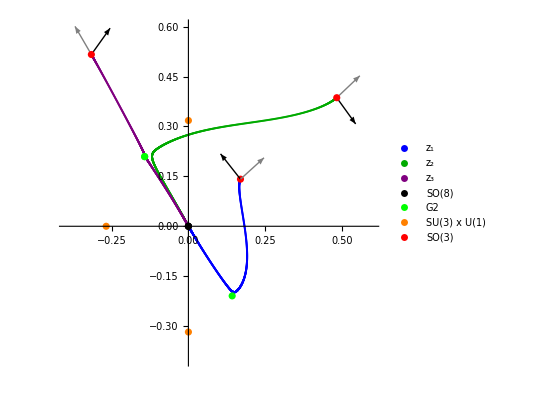

```mathematica
(* Get the x and y values, save them as "coordinates *)
vals =Re[funcs/. r ->Subdivide[rmax, 1000]];
{x1vals,y1vals,x2vals,y2vals,x3vals,y3vals} = Table[vals[[i]][[1]],{i,1,6}];
{vals1,vals2,vals3}={Transpose@{x1vals,y1vals},Transpose@{x2vals,y2vals},Transpose@{x3vals,y3vals}};
plotComplexScalars=ListPlot[{vals1,vals2,vals3},mystyle];
Show[plotComplexScalars,plotCriticalPoints,plotArrows4]
```

# Archive: generalizing BPS equations etc to seven scalars

```mathematica
(*zprime1SSIm=Table[-Sqrt[2]*Exp[kahlerpotSevenScalars/2]*(superpotSevenScalars/Abs[superpotSevenScalars])*Sum[Inverse[kahlerMetricSevenScalars][[a]][[b]]*nablaBarSS[conjugate[superpotSevenScalars]][[b]],{b,1,7}],{a,1,7}]//complexToRealScalarsIm//refine//ExpToTrig; *)
(*zprime1SSIm=zprime1SSIm/.{im^2->-1};*)
(*Put[zprime1SSIm, "zprime1SSIm"]; *)
```

```mathematica
(*zprime1SSIm=Get["zprime1SSIm"];*)
(*zprime1SS=Get["zprime1SS"];*)
```

```mathematica
(* BREAKS MATHEMATICA; Now do the complex expand part *)
(*zprimeSSIm=Assuming[assumptions,ComplexExpand[zprime1SSIm]]*)
```

```mathematica
(*zprimeSuperpotentialPart=ComplexExpand[complexToRealScalars[superpotSevenScalars]]/Conjugate[ComplexExpand[complexToRealScalars[superpotSevenScalars]]]//ComplexExpand;*)
```

```mathematica
(*zprimeScalarPart=-Sqrt[2]*ComplexExpand[complexToRealScalars[Exp[kahlerpotSevenScalars]]]*zprimeSuperpotentialPart//ComplexExpand //Simplify(* what Bobev called "T" *)*)
```

```mathematica
(* Save it *)
(*zprimeT=zprimeScalarPart;*)
(*Put[zprimeT,"zprimeT"];*)
zprimeT=Get["zprimeT"];
```

```mathematica
(* Write T = P + iQ *)
(*zprimeP=Re[zprimeT]//ComplexExpand;*)
(*zprimeQ=Im[zprimeT]//ComplexExpand;*)
```

```mathematica
(*zprimeP=zprimeP//Simplify;*)
(*zprimeQ=zprimeQ//Simplify;*)
```

```mathematica
(*Put[zprimeP,"zprimeP"]*)
(*Put[zprimeQ,"zprimeQ"]*)
```

```mathematica
(*zprimeP=Get["zprimeP"];*)
(*zprimeQ=Get["zprimeQ"];*)
```

```mathematica
(* Now get the "vector part" *)
(*zprimeS=Table[Sum[Inverse[ComplexExpand[complexToRealScalars[kahlerMetricSevenScalars]]][[a]][[b]]*ComplexExpand[complexToRealScalars[nablaBarSS[ComplexExpand[complexToRealScalars[conjugate[superpotSevenScalars]]]]]][[b]],{b,1,7}],{a,1,7}]*)
```

```mathematica
(*invMetric=Inverse[kahlerMetricSevenScalars]//complexToRealScalars//ComplexExpand//FS*)
```

```mathematica
(*nablaPart=nablaBarSS[conjugate[superpotSevenScalars]]//complexToRealScalars//ComplexExpand//Simplify*)
```

```mathematica
(*zprimeS=Table[Sum[invMetric[[a]][[b]]*nablaPart[[b]],{b,1,7}],{a,1,7}]//Simplify//ComplexExpand*)
(*Put[zprimeS,"zprimeS"]*)
```

```mathematica
zprimeS=Get["zprimeS"];
```

```mathematica
(*zprimeU=Re[zprimeS]//ComplexExpand//Simplify;*)
(*zprimeV=Im[zprimeS]//ComplexExpand//Simplify;*)
(*Put[zprimeU,"zprimeU"];*)
(*Put[zprimeV,"zprimeV"];*)
```

## Get results

```mathematica
zprimeSRe=zprimeS//Re//ComplexExpand//Simplify;
zprimeSIm=zprimeS//Im//ComplexExpand//Simplify;
```

```mathematica
(*Put[zprimeSRe,"zprimeSRe"]*)
(*Put[zprimeSIm,"zprimeSIm"]*)
```

```mathematica
zprimeSRe=Get["zprimeSRe"];
zprimeSIm=Get["zprimeSIm"];
```

```mathematica
zprimeSqrtT=Sqrt[zprimeT];
zprimeSqrtTRe=Re[zprimeSqrtT]//ComplexExpand//Simplify;
zprimeSqrtTIm=Im[zprimeSqrtT]//ComplexExpand//Simplify;
```

$Aborted

$Aborted

```mathematica
zprimeSS=zprimeS*Sqrt[zprimeT];
zprimeSSC=ComplexExpand[Conjugate[zprimeS]]*ComplexExpand[Conjugate[Sqrt[zprimeT]]];
```

```mathematica
Put[zprimeSS,"zprimeSS"]
Put[zprimeSSC,"zprimeSSC"]
```

```mathematica
(* Test *)
point=Table[12,14];
zprimeSS/.Table[sigma[[i]]->point[[i]],{i,1,14}];
%//N
zprimeSSC/.Table[sigma[[i]]->point[[i]],{i,1,14}];
%//N
```

{-10.5936-14.1839 ⅈ,-10.5936-14.1839 ⅈ,-10.5936-14.1839 ⅈ,-10.5936-14.1839 ⅈ,-10.5936-14.1839 ⅈ,-10.5936-14.1839 ⅈ,-10.5936-14.1839 ⅈ}

{-10.5936+14.1839 ⅈ,-10.5936+14.1839 ⅈ,-10.5936+14.1839 ⅈ,-10.5936+14.1839 ⅈ,-10.5936+14.1839 ⅈ,-10.5936+14.1839 ⅈ,-10.5936+14.1839 ⅈ}

## Mess:

```mathematica
xprimeSS=Re[zprimeSS]//ComplexExpand;
```

```mathematica
yprimeSS=Im[zprimeSS]//ComplexExpand;
```

```mathematica
Put[xprimeSS,"xprimeSS"]
Put[yprimeSS,"yprimeSS"]
```

```mathematica
xprimeSSSimplified=xprimeSS//Simplify;
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
yprimeSSSimplified=yprimeSS//Simplify;
```

```mathematica
Put[xprimeSSSimplified,"xprimeSSSimplified"]
Put[yprimeSSSimplified,"yprimeSSSimplified"]
```

# Do another attempt at this

```mathematica
zprime1SSNew=Table[-Sqrt[2]*Exp[kahlerpotSevenScalars/2]*(superpotSevenScalars/Abs[superpotSevenScalars])*Sum[Inverse[kahlerMetricSevenScalars][[a]][[b]]*nablaBarSS[conjugate[superpotSevenScalars]][[b]],{b,1,7}],{a,1,7}]//complexToRealScalars//refine; 
zbprime1SSNew=Table[-Sqrt[2]*Exp[kahlerpotSevenScalars/2]*(conjugate[superpotSevenScalars]/Abs[superpotSevenScalars])*Sum[Inverse[kahlerMetricSevenScalars][[a]][[b]]*nablaSS[superpotSevenScalars][[b]],{b,1,7}],{a,1,7}]//complexToRealScalars//refine; 
zprime1SSCNew=Table[-Sqrt[2]*Exp[kahlerpotSevenScalars/2]*(superpotSevenScalars/Abs[superpotSevenScalars])*Sum[Inverse[kahlerMetricSevenScalars][[a]][[b]]*nablaBarSS[conjugate[superpotSevenScalars]][[b]],{b,1,7}],{a,1,7}]//conjugate//complexToRealScalars//refine; 
(*zprime1SSIm=zprime1SSIm/.{im^2->-1};*)
Put[zprime1SSNew, "zprime1SSNew"]; 
Put[zbprime1SSNew, "zbprime1SSNew"]; 
Put[zprime1SSCNew, "zprime1SSCNew"];
```

```mathematica
(*zprime1SSIm=Get["zprime1SSIm"];*)
(*zprime1SS=Get["zprime1SS"];*)
```

```mathematica
(* BREAKS MATHEMATICA; Now do the complex expand part *)
(*zprimeSSIm=Assuming[assumptions,ComplexExpand[zprime1SSIm]]*)
```

```mathematica
(*zprimeSuperpotentialPart=ComplexExpand[complexToRealScalars[superpotSevenScalars]]/Conjugate[ComplexExpand[complexToRealScalars[superpotSevenScalars]]]//ComplexExpand;*)
```

```mathematica
(*zprimeScalarPart=-Sqrt[2]*ComplexExpand[complexToRealScalars[Exp[kahlerpotSevenScalars]]]*zprimeSuperpotentialPart//ComplexExpand //Simplify(* what Bobev called "T" *)*)
```

```mathematica
(* Save it *)
(*zprimeT=zprimeScalarPart;*)
(*Put[zprimeT,"zprimeT"];*)
zprimeT=Get["zprimeT"];
```

```mathematica
(* Write T = P + iQ *)
(*zprimeP=Re[zprimeT]//ComplexExpand;*)
(*zprimeQ=Im[zprimeT]//ComplexExpand;*)
```

```mathematica
(*zprimeP=zprimeP//Simplify;*)
(*zprimeQ=zprimeQ//Simplify;*)
```

```mathematica
(*Put[zprimeP,"zprimeP"]*)
(*Put[zprimeQ,"zprimeQ"]*)
```

```mathematica
(*zprimeP=Get["zprimeP"];*)
(*zprimeQ=Get["zprimeQ"];*)
```

```mathematica
(* Now get the "vector part" *)
(*zprimeS=Table[Sum[Inverse[ComplexExpand[complexToRealScalars[kahlerMetricSevenScalars]]][[a]][[b]]*ComplexExpand[complexToRealScalars[nablaBarSS[ComplexExpand[complexToRealScalars[conjugate[superpotSevenScalars]]]]]][[b]],{b,1,7}],{a,1,7}]*)
```

```mathematica
(*invMetric=Inverse[kahlerMetricSevenScalars]//complexToRealScalars//ComplexExpand//FS*)
```

```mathematica
(*nablaPart=nablaBarSS[conjugate[superpotSevenScalars]]//complexToRealScalars//ComplexExpand//Simplify*)
```

```mathematica
(*zprimeS=Table[Sum[invMetric[[a]][[b]]*nablaPart[[b]],{b,1,7}],{a,1,7}]//Simplify//ComplexExpand*)
(*Put[zprimeS,"zprimeS"]*)
```

```mathematica
zprimeS=Get["zprimeS"];
```

```mathematica
(*zprimeU=Re[zprimeS]//ComplexExpand//Simplify;*)
(*zprimeV=Im[zprimeS]//ComplexExpand//Simplify;*)
(*Put[zprimeU,"zprimeU"];*)
(*Put[zprimeV,"zprimeV"];*)
```

## Real and imag

```mathematica
xprimeSSNew=Re[zprime1SSNew]//ComplexExpand//refine;
```

```mathematica
yprimeSSNew=Im[zprime1SSNew]//ComplexExpand//refine;
```

```mathematica
Put[xprimeSSNew,"xprimeSSNew"]
Put[yprimeSSNew,"yprimeSSNew"]
```

## Trying something else

```mathematica
kahlerPrefactor=Exp[complexToRealScalars[kahlerpotSevenScalars]/2]//Simplify;
```

```mathematica
ce[func_]:=(ComplexExpand[complexToRealScalars[func]]);
cce[func_]:=(ComplexExpand[complexToRealScalars[conjugate[func]]]);
```

```mathematica
zprimeSSExpanded=Table[-Sqrt[2]*kahlerPrefactor*(ce[superpotSevenScalars]/Sqrt[ce[superpotSevenScalars]ce[conjugate[superpotSevenScalars]]])*Sum[ce[Inverse[kahlerMetricSevenScalars][[a]][[b]]]*ce[nablaBarSS[conjugate[superpotSevenScalars]]][[b]],{b,1,7}],{a,1,7}]//complexToRealScalars//refine;
```

```mathematica
zprimeSSCExpanded=Table[-Sqrt[2]*kahlerPrefactor*(cce[superpotSevenScalars]/Sqrt[cce[superpotSevenScalars]cce[conjugate[superpotSevenScalars]]])*Sum[cce[Inverse[kahlerMetricSevenScalars][[a]][[b]]]*cce[nablaBarSS[conjugate[superpotSevenScalars]]][[b]],{b,1,7}],{a,1,7}]//complexToRealScalars//refine;
```

```mathematica
Put[zprimeSSExpanded, "zprimeSSExpanded"]
Put[zprimeSSCExpanded, "zprimeSSCExpanded"]
```

## Real and imag:

```mathematica
zprimeSSExpanded[[1]];
```

```mathematica
xprimeSSExpanded=Re[zprimeSSExpanded]//ComplexExpand//refine;
```

$Aborted

```mathematica
yprimeSSExpanded=Im[zprimeSSExpanded]//ComplexExpand//refine;
```

```mathematica
Put[xprimeSSExpanded,"xprimeSSExpanded"]
Put[yprimeSSExpanded,"yprimeSSExpanded"]
```

## Take real and imaginary part “by hand”

```mathematica
(* Now expanded versions *)
xprimeSSE=1/2(zprimeSSExpanded+zprimeSSCExpanded)//ComplexExpand;
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

$Aborted

```mathematica
yprimeSSE=-I/2(zprimeSSExpanded-zprimeSSCExpanded)//ComplexExpand;
sigmaprimeSSE={xprimeSSE,yprimeSSE}//Transpose//Flatten;
```

```mathematica
Put[xprimeSSExpanded,"xprimeSSExpanded"]
Put[yprimeSSExpanded,"yprimeSSExpanded"]
```

## Eigenvalues and eigenvectors in 3 scalar model (not relevant anymore)

```mathematica
(* Load the Jacobian from earlier. This takes around a minute or something to load. *)
(* jacobian = Get["jacobian"]; *)
```

#### First critical point

```mathematica
(* Select the critical point at which we want to evaluate *)
index=1;
fp = critPoints[[index]];
fpSigma=critPointsSigma[[index]];
potentialValue=potentialValuesCrits[[index]];
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
```

```mathematica
(* Load the Jacobian matrix again *)
jacobianCrit1Num=Get["jacobianCrit1Num"];
```

```mathematica
eigensystem1=Eigensystem[jacobianCrit1Num];
{eigenvals1,eigenvecs1}=eigensystem1;
L=Sqrt[-3/potentialValue];
deltas1=-L*eigenvals1;
(* Print deltas for comparison, see if they are OK*)
{deltas1,eigenvecs1}
Put[eigensystem1,"eigensystem1"];
```

{{1.,1.,1.,1.,1.,1.},{{1.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.},{0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,1.}}}

#### Save everything together:

```mathematica
{jacobianCrit1Num,jacobianCrit2Num,jacobianCrit3Num,jacobianCrit4Num}={Get["jacobianCrit1Num"],Get["jacobianCrit2Num"],Get["jacobianCrit3Num"],Get["jacobianCrit4Num"]};
jacobiansNum={jacobianCrit1Num,jacobianCrit2Num,jacobianCrit3Num,jacobianCrit4Num};
(*eigenvecs={eigenvecs1,eigenvecs2,eigenvecs3,eigenvecs4};*)
(*eigenvals = {eigenvals1,eigenvals2,eigenvals3,eigenvals4};*)
(* Save, for each of the critical points, the indices corresponding to the modes that 'repel' *)
indexModesAll={{},{2},{3,6},{3,4}};
```

```mathematica
(* To plot the critical points, we have to pair them like {{x1, y1}, {x2, y2},...} *)
critPointsSigmaCut=Table[critPointsSigma[[i]]//cut,{i,1,Length[critPointsSigma]}];
(* Define already a way to plot *)
plotCriticalPoints=ListPlot[critPointsSigmaCut,mystyleCrit];
```

## Extra: getting the masses and checking which are turned on by the BPS equations

```mathematica
potential2RF=potentialSevenScalars//complexToRealScalars;
doubleDvPot=Table[Table[D[D[potential2RF,sigma[[i]]],sigma[[j]]],{i,1,Length[sigma]}],{j,1,Length[sigma]}];
```

#### #1

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=1;
fp = critPointsSevenScalars[[index]];
potentialValue=potentialValues[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetricSevenScalars//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop
distinctMasses=allMasses//DeleteDuplicates
```

{-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.,-2.}

{-2.}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
distinctDeltaSolutions=Table[Solve[distinctMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[distinctMasses]}];
distinctDeltas=Table[deltaVector[[i]]/.distinctDeltaSolutions[[i]],{i,1,Length[distinctDeltaSolutions]}]
```

{{1.,2.}}

```mathematica
(* What do the BPS equations give? *)
jac=getJacobian[fpSigma]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[scaleSquared]/.{g->1};
deltas=eigenvals*(-L);
deltas//N
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

#### #2

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=2;
fp = critPointsSevenScalars[[index]];
potentialValue=potentialValues[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetricSevenScalars//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.24158,-2.24158,-2.24158,-2.24158,-2.24158,-2.24158,-1.42509,-1.42509,-1.42509,-1.42509,-1.42509,-1.42509,1.55051,6.44949}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{1.40825,1.59175},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{0.591752,2.40825},{-0.44949,3.44949},{-1.44949,4.44949}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.59175,1.59175,1.59175,1.59175,1.59175,1.59175,2.40825,2.40825,2.40825,2.40825,2.40825,2.40825,3.44949,4.44949}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.40825,1.40825,1.40825,1.40825,1.40825,1.40825,0.591752,0.591752,0.591752,0.591752,0.591752,0.591752,-0.44949,-1.44949}

```mathematica
(* What do the BPS equations give? *)
jac=getJacobian[fpSigma]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[scaleSquared]/.{g->1};
deltas=eigenvals*(-L);
deltas//N
```

{3.44949,-1.44949,1.40825,1.40825,1.40825,1.40825,1.40825,1.40825,0.591752,0.591752,0.591752,0.591752,0.591752,0.591752}

#### #3

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=3;
fp = critPointsSevenScalars[[index]];
potentialValue=potentialValues[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetricSevenScalars//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=mlSquared2Crit2=Eigenvalues[mlMatrix]//Chop //Sort
```

{-2.22222,-2.22222,-2.22222,-2.,-2.,-2.,-2.,-1.55556,-1.55556,-1.55556,-1.12311,2.,2.,7.12311}

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.33333,1.66667},{1.33333,1.66667},{1.33333,1.66667},{1.,2.},{1.,2.},{1.,2.},{1.,2.},{0.666667,2.33333},{0.666667,2.33333},{0.666667,2.33333},{0.438447,2.56155},{-0.561553,3.56155},{-0.561553,3.56155},{-1.56155,4.56155}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.66667,1.66667,1.66667,2.,2.,2.,2.,2.33333,2.33333,2.33333,2.56155,3.56155,3.56155,4.56155}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.33333,1.33333,1.33333,1.,1.,1.,1.,0.666667,0.666667,0.666667,0.438447,-0.561553,-0.561553,-1.56155}

```mathematica
(* What do the BPS equations give? *)
jac=getJacobian[fpSigma]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[scaleSquared]/.{g->1};
deltas=eigenvals*(-L);
deltas//N
```

{3.56155,2.56155,-1.56155,1.33333,1.33333,1.33333,1.,1.,1.,1.,0.666667,0.666667,0.666667,-0.561553}

#### #4

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=4;
fp = critPointsSevenScalars[[index]];
potentialValue=potentialValues[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetricSevenScalars//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=mlSquared2Crit2=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.24473,-2.24473,-2.18813,-1.6856,-1.09949,-1.09949,-0.108916,-0.108916,2.66206,3.81757,3.81757,8.09469,8.65678,16.2619}

```mathematica
-1.6856013743161378
```

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.42738,1.57262},{1.42738,1.57262},{1.25126,1.74874},{0.748735,2.25126},{0.427383,2.57262},{0.427383,2.57262},{0.0367557,2.96324},{0.0367557,2.96324},{-0.716316,3.71632},{-0.963244,3.96324},{-0.963244,3.96324},{-1.71632,4.71632},{-1.80254,4.80254},{-2.80254,5.80254}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.57262,1.57262,1.74874,2.25126,2.57262,2.57262,2.96324,2.96324,3.71632,3.96324,3.96324,4.71632,4.80254,5.80254}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.42738,1.42738,1.25126,0.748735,0.427383,0.427383,0.0367557,0.0367557,-0.716316,-0.963244,-0.963244,-1.71632,-1.80254,-2.80254}

```mathematica
(* What do the BPS equations give? *)
jac=getJacobian[fpSigma]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[scaleSquared]/.{g->1};
deltas=eigenvals*(-L);
deltas//N
```

{4.80254,3.71632,2.96324,2.96324,-2.80254,-1.71632,1.57262,1.57262,1.25126,-0.963244,-0.963244,0.748735,0.427383,0.427383}

#### #5

```mathematica
(* Choose the critical point at which we want to evaluate and define auxiliary functions *)
index=5;
fp = critPointsSevenScalars[[index]];
potentialValue=potentialValues[[index]];
fpRe=Re[fp];
fpIm=Im[fp];
(* Now organize it like sigma: x1, y1, x2, y2,... *)
fpSigma=Transpose[{fpRe,fpIm}]//Flatten;
evalatFP[f_]:= f/. Table[sigma[[i]]->N[fpSigma[[i]]],{i,1,Length[sigma]}];
(* Get the 14 x 14 kinetic matrix and its inverse *)
kineticMatrixDiagonalV1=kahlerMetricSevenScalars//complexToRealScalars//ComplexExpand//Diagonal;
kineticMatrixDiagonal=Table[{kineticMatrixDiagonalV1[[i]],kineticMatrixDiagonalV1[[i]]},{i,1,7}]//Flatten;
kineticMatrix=DiagonalMatrix[kineticMatrixDiagonal];
invKineticMatrix=Inverse[kineticMatrix];
(* Get the mass matrix from it and diagonalize it *)
massMatrix=0.5*invKineticMatrix.doubleDvPot//evalatFP;
massMatrixNum=massMatrix//N//refine//Chop;
massMatrixNum//MatrixForm;
scaleSquared=-3/potentialValue;
mlMatrix=massMatrixNum*scaleSquared/.{g->1,c->1};
allMasses=mlSquared2Crit2=Eigenvalues[mlMatrix]//Chop//Sort
```

{-2.22938,-2.22938,-2.19615,-2.,-2.,-1.51659,-1.51659,-0.732051,2.73205,3.0671,3.0671,8.19615,8.67887,8.67887}

```mathematica
3.0670996447316408
```

```mathematica
(* Get deltas *)
deltaVector={Δ,Δ};
deltaSolutions=Table[Solve[allMasses[[i]]-Δ(Δ-3)==0,Δ],{i,1,Length[allMasses]}];
allDeltas=Table[Table[deltaVector[[j]]/.deltaSolutions[[i]][[j]],{j,1,2}],{i,1,Length[deltaSolutions]}]
```

{{1.35639,1.64361},{1.35639,1.64361},{1.26795,1.73205},{1.,2.},{1.,2.},{0.643606,2.35639},{0.643606,2.35639},{0.267949,2.73205},{-0.732051,3.73205},{-0.805884,3.80588},{-0.805884,3.80588},{-1.73205,4.73205},{-1.80588,4.80588},{-1.80588,4.80588}}

```mathematica
deltaPlus=Table[Max[allDeltas[[i]]],{i,1,14}]
```

{1.64361,1.64361,1.73205,2.,2.,2.35639,2.35639,2.73205,3.73205,3.80588,3.80588,4.73205,4.80588,4.80588}

```mathematica
deltaMinus=Table[Min[allDeltas[[i]]],{i,1,14}]
```

{1.35639,1.35639,1.26795,1.,1.,0.643606,0.643606,0.267949,-0.732051,-0.805884,-0.805884,-1.73205,-1.80588,-1.80588}

```mathematica
(* What do the BPS equations give? *)
jac=getJacobian[fpSigma]/.{g->1};
{eigenvals, eigenvecs}=Eigensystem[jac];
(* Quickly check the deltas to see if we got the right expansion? *)
potentialValue=potentialValues[[index]]/.{g->1};
L=Sqrt[scaleSquared]/.{g->1};
deltas=eigenvals*(-L);
deltas//N
```

{3.80588,3.80588,3.73205,-1.80588,-1.80588,1.73205,-1.73205,1.35639,1.35639,1.,1.,0.643606,0.643606,0.267949}